```mathematica
Lecture 6:Modules, Recursion
```

## Modules and local variables

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
Clear[n,k];
n=6;
Module[{k=4,j=0},n=n+k;Range@15;n^2]
{n,k,j}
```

100

{10,k,j}

### Exercise Subsection

```mathematica
Clear[f]
```

What does the following cell do when evaluated?

```mathematica
f[L_List]:=Module[{A=L/.{x_/;Positive[x]->1,x_/;Negative[x]->-1}},
And[FreeQ[A,{___,1,1,___}],FreeQ[A,{___,-1,-1,___}]]]
```

## Recursions

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
Clear[f]
f[n_]:=Which[n==0,1,n==1,1,True,f[n-1]+f[n-2]]
f/@Range@10
```

{1,2,3,5,8,13,21,34,55,89}

```mathematica
f[3/2]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -2041/2==0.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Hold[-2041/2==0].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Hold[Hold[-2041/2==0]].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

$Aborted

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
f[n_Integer/;n>=0]:=If[n<=1,1,n f[n-1]]
f/@Range@10
```

### Exercise Subsection

Recall from Exercise Set 4 that a Gray code (see https://en.wikipedia.org/wiki/Gray_code ) is an ordering of all bit strings (which are lists with elements either 0 or 1) such that consecutive bit strings differ in exactly one position.  Using the idea outlined in Set 4, we can recursively define a gray code; see this example:

```mathematica
GrayCode[n_]:=If[n==0,{{}},Join[Prepend[#,0]&/@GrayCode[n-1],Prepend[#,1]&/@Reverse@GrayCode[n-1]]]
```

```mathematica
GrayCode[3]
```

{{0,0,0},{0,0,1},{0,1,1},{0,1,0},{1,1,0},{1,1,1},{1,0,1},{1,0,0}}

### Exercise Subsection

The Euclidean algorithm finds the greatest common divisor of a and b recursively.  Write down the values iteratively taken by a and b in the recursion below when starting with a=13 and b=21.

```mathematica
Euclidean[a_,b_]:=If[b==0,a,Print[{a,b}];Euclidean[b,Mod[a,b]]]
```

```mathematica
Euclidean[13,21]
```

{13,21}

{21,13}

{13,8}

{8,5}

{5,3}

{3,2}

{2,1}

1

```mathematica
Fibonacci@Range@10
```

{1,1,2,3,5,8,13,21,34,55}

### Exercise Subsection

Define a recursive function named MergeLists[L1_,L2_,L3_:{}] that takes in three lists L1, L2, and L3 (as an optional argument that defaults to {}) of nondecreasing numbers and outputs the sorted list with the numbers found in L1 an L2. The function should do the following:

1. Find the smaller of the two first elements in L1 and L2, say s.
2. Remove s from L1 (or L2) and append s to L3.
2. Repeat until both L1 and L2 are empty, then return L3.

No built-in sorting operations can be used to do this exercise.

```mathematica
MergeLists[L1_List/;FreeQ[{___,a_,b_,___}/;a>b],L2_List,L3_:{}]:=
If[L1=={}||L2=={},Join[L3,L1,L2],
If[First@L1<=First@L2,
MergeLists[Rest@L1,L2,Append[L3,First@L1]],
MergeLists[L1,Rest@L2,Append[L3,First@L2]]]]
```

```mathematica
MergeLists[{1,1,2},{2,2,2,3}]
```

{1,1,2,2,2,2,3}

```mathematica
{4,1}
```

### Exercise Subsection

Merge sort (see https://en.wikipedia.org/wiki/Merge_sort ) is is a divide and conquer algorithm for sorting a list of numbers.  It works on the list L by 

1. Returning L in the case when L contains only one element, 
2. Merging (using the MergeLists function defined in the previous exercise) the list L[[;;1]] of length 1 containing only the first element on L and the Mergesort -ed list L[[2;;]].

Create a recursive function called Mergesort[L_List] that takes a list L as an input and returns the list in nondecreasing order.  You may not use any built-in sorting operations.

```mathematica
Mergesort[L_List]:=If[Length@L<=1,L,MergeLists[L[[;;1]],Mergesort@L[[2;;]]]]
```

```mathematica
Mergesort[{4,2,5,7,2,7,2,5,5}]
```

{2,2,2,4,5,5,5,7,7}

## Memoization

### Exercise Subsection

The Pell numbers are defined by P_0=0, P_1= 1 and P_n= 2 P_(n-1)+P_(n-2) for n ≥ 2.  Write a recursive function Pell that returns P_n and then verify that

P_n= ((1 + √2)^n- (1 - √2)^n)/(2 √2)

holds for 0 ≤n ≤ 100.  The function Pell should take advantage of memoization.

```mathematica
Clear[Pell]
```

```mathematica
Pell[n_]:=Pell[n]=If[n<=1,n,2 Pell[n-1]+Pell[n-2]]
```

```mathematica
Pell[20]
```

15994428

```mathematica
Timing[Pell/@Range@1000]
```

{0.006023,{1,2,5,12,29,70,169,408,985,2378,5741,13860,33461,80782,195025,470832,1136689,2744210,6625109,15994428,38613965,93222358,225058681,543339720,1311738121,3166815962,7645370045,18457556052,44560482149,107578520350,259717522849,627013566048,1513744654945,3654502875938,8822750406821,21300003689580,51422757785981,124145519261542,299713796309065,723573111879672,1746860020068409,4217293152016490,10181446324101389,24580185800219268,59341817924539925,143263821649299118,345869461223138161,835002744095575440,2015874949414289041,4866752642924153522,11749380235262596085,28365513113449345692,68480406462161287469,165326326037771920630,399133058537705128729,963592443113182178088,2326317944764069484905,5616228332641321147898,13558774610046711780701,32733777552734744709300,79026329715516201199301,190786436983767147107902,460599203683050495415105,1111984844349868137938112,2684568892382786771291329,6481122629115441680520770,15646814150613670132332869,37774750930342781945186508,91196316011299234022705885,220167382952941249990598278,531531081917181734003902441,1283229546787304717998403160,3097990175491791170000708761,7479209897770887057999820682,18056409971033565286000350125,43592029839838017630000520932,105240469650709600546001391989,254072969141257218722003304910,613386407933224037990008001809,1480845785007705294702019308528,3575077977948634627394046618865,8631001740904974549490112546258,20837081459758583726374271711381,50305164660422142002238655969020,121447410780602867730851583649421,293199986221627877463941823267862,707847383223858622658735230185145,1708894752669345122781412283638152,4125636888562548868221559797461449,9960168529794442859224531878561050,24045973948151434586670623554583549,58052116426097312032565778987728148,140150206800346058651802181530039845,338352530026789429336170142047807838,816855266853924917324142465625655521,1972063063734639263984455073299118880,4760981394323203445293052612223893281,11494025852381046154570560297746905442,27749033099085295754434173207717704165,66992092050551637663438906713182313772,161733217200188571081311986634082331709,390458526450928779826062879981346977190,942650270102046130733437746596776286089,2275759066655021041292938373174899549368,5494168403412088213319314492946575384825,13264095873479197467931567359068050319018,32022360150370483149182449211082676022861,77308816174220163766296465781233402364740,186639992498810810681775380773549480752341,450588801171841785129847227328332363869422,1087817594842494380941469835430214208491185,2626223990856830547012786898188760780851792,6340265576556155474967043631807735770194769,15306755143969141496946874161804232321241330,36953775864494438468860791955416200412677429,89214306872958018434668458072636633146596188,215382389610410475338197708100689466705869805,519979086093778969111063874274015566558335798,1255340561797968413560325456648720599822541401,3030660209689715796231714787571456766203418600,7316660981177400006023755031791634132229378601,17663982172044515808279224851154725030662175802,42644625325266431622582204734101084193553730205,102953232822577379053443634319356893417769636212,248551090970421189729469473372814871029093002629,600055414763419758512382581064986635475955641470,1448661920497260706754234635502788141981004285569,3497379255757941172020851852070562919437964212608,8443420432013143050795938339643913980856932710785,20384220119784227273612728531358390881151829634178,49211860671581597598021395402360695743160591979141,118807941462947422469655519336079782367473013592460,286827743597476442537332434074520260478106619164061,692463428657900307544320387485120303323686251920582,1671754600913277057625973209044760867125479123005225,4035972630484454422796266805574642037574644497931032,9743699861882185903218506820194044942274768118867289,23523372354248826229233280445962731922124180735665610,56790444570379838361685067712119508786523129590198509,137104261495008502952603415870201749495170439916062628,330998967560396844266891899452523007776864009422323765,799102196615802191486387214775247765048898458760710158,1929203360792001227239666329003018537874660926943744081,4657508918199804645965719872781284840798220312648198320,11244221197191610519171106074565588219471101552240140721,27145951312583025684307932021912461279740423417128479762,65536123822357661887786970118390510778951948386497100245,158218198957298349459881872258693482837644320190122680252,381972521736954360807550714635777476454240588766742460749,922163242431207071074983301530248435746125497723607601750,2226299006599368502957517317696274347946491584213957664249,5374761255629944076990017936922797131639108666151522930248,12975821517859256656937553191541868611224708916517003524745,31326404291348457390865124320006534354088526499185529979738,75628630100556171438667801831554937319401761914888063484221,182583664492460800268200727983116408992892050328961656948180,440795959085477771975069257797787755305185862572811377380581,1064175582663416344218339243578691919603263775474584411709342,2569147124412310460411747744955171594511713413521980200799265,6202469831488037265041834733489035108626690602518544813307872,14974086787388384990495417211933241811765094618559069827415009,36150643406264807246032669157355518732156879839636684468137890,87275373599917999482560755526644279276078854297832438763690789,210701390606100806211154180210644077284314588435301561995519468,508678154812119611904869115947932433844708031168435562754729725,1228057700230340030020892412106508944973730650772172687504978918,2964793555272799671946653940160950323792169332712780937764687561,7157644810775939373914200292428409592558069316197734563034354040,17280083176824678419775054525017769508908307965108250063833395641,41717811164425296213464309342463948610374685246414234690701145322,100715705505675270846703673209945666729657678457936719445235686285,243149222175775837906871655762355282069690042162287673581172517892,587014149857226946660446984734656230869037762782512066607580722069,1417177521890229731227765625231667743807765567727311806796333962030,3421369193637686409115978235197991718484568898237135680200248646129,8259915909165602549459722095627651180776903364201583167196831254288,19941201011968891508035422426453294080038375626640302014593911154705,48142317933103385565530566948534239340853654617482187196384653563698,116225836878175662639096556323521772761745684861604676407363218282101,280593991689454710843723679595577784864345024340691540011111090127900,677413820257085084326543915514677342490435733542987756429585398537901,1635421632203624879496811510624932469845216491426667052870281887203702,3948257084664334843320166936764542282180868716396321862170149172945305,9531935801532294566137145384154017034206953924219310777210580233094312,23012128687728923975594457705072576350594776564834943416591309639133929,55556193176990142517326060794299169735396507053889197610393199511362170,134124515041709209010246579293670915821387790672613338637377708661858269,323805223260408560537819219381641001378172088399115874885148616835078708,781734961562526330085885018056952918577731967470845088407674942332015685,1887275146385461220709589255495546838533636023340806051700498501499110078,4556285254333448771505063529048046595645004014152457191808671945330235841,10999845655052358763719716313591640029823644051645720435317842392159581760,26555976564438166298944496156231326655292292117443898062444356729649399361,64111798783928691361608708626054293340408228286533516560206555851458380482,154779574132295549022161913408339913336108748690510931182857468432566160325,373670947048519789405932535442734120012625725667555378925921492716590701132,902121468229335127834026984293808153361360200025621689034700453865747562589,2177913883507190045073986504030350426735346125718798756995322400448085826310,5257949235243715217981999992354509006832052451463219203025345254761919215209,12693812353994620481037986488739368440399451028645237163046012909971924256728,30645573943232956180057972969833245887630954508753693529117371074705767728665,73984960240460532841153932428405860215661360046152624221280755059383459714058,178615494424154021862365837826644966318953674601058941971678881193472687156781,431215949088768576565885608081695792853568709248270508164638517446328834027620,1041047392601691174994137053990036552026091093097599958300955916086130355212021,2513310734292150926554159716061768896905750895443470424766550349618589544451662,6067668861185993028102456486113574345837592883984540807834056615323309444115345,14648648456664136982759072688288917588580936663412552040434663580265208432682352,35364965774514266993620601862691409522999466210809644888703383775853726309480049,85378580005692670970000276413671736634579869085031841817841431131972661051642450,206122125785899608933621154690034882792159204380873328524386246039799048412764949,497622831577491888837242585793741502218898277846778498866613923211570757877172348,1201367788940883386608106326277517887229955760074430326257614092462940564167109645,2900358409459258662053455238348777276678809797995639151381842108137451886211391638,7002084607859400710715016802975072440587575356065708629021298308737844336589892921,16904527625178060083483488844298922157853960510127056409424438725613140559391177480,40811139858215520877681994491572916756295496376319821447870175759964125455372247881,98526807341609101838847477827444755670444953262766699305164790245541391470135673242,237864754541433724555376950146462428097185402901853220058199756251046908395643594365,574256316424476550949601378120369611864815759066473139421564302747635208261422861972,1386377387390386826454579706387201651826816921034799498901328361746317324918489318309,3347011091205250203858760790894772915518449601136072137224221026240269858098401498590,8080399569800887234172101288176747482863716123306943773349770414226857041115292315489,19507810230807024672202963367248267881245881847749959683923761854693983940328986129568,47096020031414936578578028022673283245355479818806863141197294123614824921773264574625,113699850293636897829359019412594834371956841485363685966318350101923633783875515278818,274495720618688732237296066847862951989269162789534235073833994327462092489524295132261,662691291531014362303951153108320738350495167064432156113986338756847818762924105543340,1599878303680717456845198373064504428690259496918398547301806671841157730015372506218941,3862447898892449275994347899237329595731014160901229250717599682439163278793669117981222,9324774101465616008833894171539163620152287818720857048737006036719484287602710742181385,22511996101823681293662136242315656836035589798342943348191611755878131853999090602343992,54348766305112978596158166656170477292223467415406743745120229548475747995600891946869369,131209528712049638485978469554656611420482524629156430838432070852829627845200874496082730,316767823729212255568115105765483700133188516673719605421984371254135003686002640939034829,764745176170474149622208681085624011686859557976595641682400813361099635217206156374152388,1846258176070160554812532467936731723506907632626910888786785997976334274120414953687339605,4457261528310795259247273616959087458700674823230417419255972809313768183458036063748831598,10760781232691751073307079701854906640908257279087745727298731616603870641036487081185002801,25978823993694297405861433020668900740517189381405908873853436042521509465531010226118837200,62718429220080345885029945743192708121942636041899563475005603701646889572098507533422677201,151415682433854989175921324507054316984402461465205035823864643445815288609728025292964191602,365549794087790324236872594757301342090747558972309635122734890593277466791554558119351060405,882515270609435637649666514021657001165897579409824306069334424632370222192837141531666312412,2130580335306661599536205622800615344422542717791958247261403739858017911177228841182683685229,5143675941222758836722077759622887690010983014993740800592141904348406044547294823897033682870,12417932217752179272980361142046390724444508747779439848445687548554830000271818488976751050969,29979540376727117382682800043715669138900000510552620497483517001458066045090931801850535784808,72377012971206414038345961229477729002244509768884680843412721551470962090453682092677822620585,174733566319139945459374722502671127143389020048321982184308960104399990225998295987206181025978,421844145609486304957095406234819983289022549865528645212030641760270942542450274067090184672541,1018421857538112555373565534972311093721434119779379272608370243624941875310898844121386550371060,2458687860685711415704226476179442170731890789424287190428771129010154693164247962309863285414661,5935797578909535386782018487331195435185215698627953653465912501645251261639394768741113121200382,14330283018504782189268263450841833041102322186680194497360596132300657216443037499792089527815425,34596363615919099765318545389014861517389860071988342648187104766246565694525469768325292176831232,83523010250342981719905354228871556075882042330656879793734805664793788605493977036442673881477889,201642384116605063205129253846757973669153944733302102235656716095834142905513423841210639939787010,486807778483553108130163861922387503414189931797261084265048237856462074416520824718863953761051909,1175257941083711279465456977691532980497533808327824270765753191808758291738555073278938547461890828,2837323660650975667061077817305453464409257548452909625796554621473978657893630971276741048684833565,6849905262385662613587612612302439909316048905233643522358862434756715607525817015832420644831557958,16537134185422300894236303041910333283041355358920196670514279490987409872945265002941582338347949481,39924173633230264402060218696123106475398759623074036863387421416731535353416347021715585321527456920,96385481451882829698356740434156546233838874605068270397289122324450480579777959046372752981402863321,232695136536995923798773699564436198943076508833210577657965666065632496512972265114461091284333183562,561775754525874677295904139563028944119991892271489425713220454455715473605722489275294935550069230445,1356246645588745278390581978690494087183060293376189429084406574977063443724417243665050962384471644452,3274269045703365234077068096944017118486112479023868283882033604409842361054556976605396860319012519349,7904784736995475746544718172578528324155285251423925996848473783796748165833531196875844683022496683150,19083838519694316727166504442101073766796682981871720277578981172003338692721619370357086226364005885649,46072461776384109200877727056780675857748651215167366552006436127803425551276769937590017135750508454448,111228762072462535128921958555662425482293985412206453381591853427610189795275159245537120497865022794545,268529985921309179458721644168105526822336622039580273315190142983023805141827088428664258131480554043538,648288733915080894046365246891873479126967229491367000011972139393657800078929336102865636760826130881621,1565107453751470967551452137951852485076271081022314273339134421770339405299685760634395531653132815806780,3778503641418022829149269522795578449279509391535995546690240982934336610678300857371656700067091762495181,9122114736587516625849991183543009383635289864094305366719616387639012626656287475377708931787316340797142,22022733114593056080849251889881597216550089119724606280129473758212361863990875808127074563641724444089465,53167580965773628787548494963306203816735468103543517926978563904063736354638039091631858059070765228976072,128357895046140313655946241816494004850021025326811642134086601566339834573266953991390790681783254902041609,309883371058054256099440978596294213516777518757166802195151767036743405501171947074413439422637275033059290,748124637162248825854828199009082431883576062841145246524390135639826645575610848140217669527057804968160189,1806132645382551907809097376614459077283929644439457295243932038316396696652393643354848778476752884969379668,4360389927927352641473022952238000586451435351720059837012254212272620038880398134849915226480563574906919525,10526912501237257190755143281090460250186800347879576969268440462861636774413189913054679231437880034783218718,25414214930401867022983309514418921086825036047479213775549135137995893587706777960959273689356323644473356961,61355342362040991236721762309928302423836872442838004520366710738853423949826745834973226610150527323729932640,148124899654483849496426834134275525934498780933155222816282556615702741487360269630905726909657378291933222241,357605141671008690229575430578479354292834434309148450152931823970258906924547285096784680429465283907596377122,863335182996501229955577695291234234520167649551452123122146204556220555336454839824475087768587946107125976485,2084275507664011150140730821160947823333169733412052696397224233082700017597456964745734855966641176121848330092,5031886198324523530237039337613129881186507116375557515916594670721620590531368769315944799701870298350822636669,12148047904313058210614809496387207585706183966163167728230413574525941198660194503377624455370381772823493603430,29327982006950639951466658330387545052598875048701892972377421819773502987851757776071193710442633843997809843529,70804011918214338113548126157162297690903934063566953672985257214072947174363710055520011876255649460819113290488,170936005843379316178562910644712140434406743175835800318347936247919397336579177887111217462953932765636036424505,412676023604972970470673947446586578559717420415238554309681129709911741847522065829742446802163514992091186139498,996288053053325257119910805537885297553841584006312908937710195667742881031623309546596111067280962749818408703501,2405252129711623484710495558522357173667400588427864372185101521045397503910768684922934668936725440491728003546500,5806792312476572226540901922582599644888642760862041653307913237758537888853160679392465448940731843733274415796501,14018836754664767937792299403687556463444686110151947678800927996562473281617090043707865566818189127958276835139502,33844465821806108102125500729957712571778014981165937010909769230883484452087340766808196582577110099649828086075505,81707768398276984142043300863602981607000716072483821700620466458329442185791771577324258731972409327257933007290512,197260002618360076386212102457163675785779447126133580412150702147542368823670883921456714046521928754165694100656529,476227773634997136914467505777930333178559610324750982524921870753414179833133539420237686825016266835589321208603570,1149715549888354350215147114013024342142898667775635545461994443654370728489937962761932087696554462425344336517863669,2775658873411705837344761733803979017464356945876022073448910758062155636813009464944101862218125191686277994244330908,6701033296711766024904670581620982377071612559527679692359815959778682002115956892650135812132804845797900325006525485,16177725466835237887154102897045943771607582064931381458168542677619519641044923250244373486483734883282078644257381878,39056484230382241799212876375712869920286776689390442608696901315017721284205803393138882785100274612362057613521289241,94290693927599721485579855648471683612181135443712266675562345307654962209456530036522139056684284108006193871299960360,227637872085581684770372587672656237144649047576814975959821591930327645703118863466183160898468842828374445356121209961,549566438098763091026325030993784157901479230597342218595205529168310253615694256968888460853621969764755084583542380282,1326770748283107866823022649660224552947607508771499413150232650266948152934507377403960082605712782357884614523205970525,3203107934664978824672370330314233263796694248140341044895670829702206559484709011776808626065047534480524313629954321332,7732986617613065516167763310288691080540996005052181502941574309671361271903925400957577334735807851318933241783114613189,18669081169891109857007896950891615424878686258244704050778819449044929103292559813691963295536663237118390797196183547710,45071148957395285230183557212071921930298368521541589604499213207761219478489045028341503925809134325555714836175481708609,108811379084681680317375011375035459285475423301327883259777245864567368060270649870374971147154931888229820469547146964928,262693907126758645864933579962142840501249215124197356124053704936895955599030344769091446220118998102015355775269775638465,634199193338198972047242171299321140287973853549722595507884655738359279258331339408557863587392928092260532020086698241858,1531092293803156589959417922560785121077196922223642547139823016413614514115693023586207173394904854286536419815443172122181,3696383780944512151966078016420891382442367697997007689787530688565588307489717386580972210377202636665333371650973042486220,8923859855692180893891573955402567885961932318217657926714884393544791129095127796748151594149310127617203163117389257094621,21544103492328873939749225927226027154366232334432323543217299475655170565679972980077275398675822891899739697885751556675462,52012066840349928773390025809854622194694396987082305013149483344855132260455073756902702391500955911416682558888892370445545,125568237173028731486529277546935271543755026308596933569516266165365435086590120493882680181677734714733104815663536297566552,303148541186407391746448580903725165282204449604276172152182015675586002433635314744668062754856425340882892190215964965578649,731865319545843514979426439354385602108163925517149277873880297516537439953860749983218805691390585396498889196095466228723850,1766879180278094421705301459612496369498532300638574727899942610708660882341356814711105674137637596133880670582406897423026349,4265623680102032358390029358579378341105228526794298733673765518933859204636574379405430153966665777664260230360909261074776548,10298126540482159138485360176771253051708989354227172195247473648576379291614505573521965982070969151462401131304225419572579445,24861876761066350635360749712121884444523207235248643124168712816086617787865585526449362118108604080589062492969360100219935438,60021880062614860409206859601015021940755403824724458443584899280749614867345676626420690218288177312640526117242945620012450321,144905636886296071453774468914151928326034014884697560011338511377585847522556938779290742554684958705870114727455251340244836080,349833153835207003316755797429318878592823433594119578466261922035921309912459554185002175327658094724380755572153448300502122481,844571944556710078087286063772789685511680882072936716943862355449428467347476047149295093210001148154631625871762147941249081042,2038977042948627159491327924974898249616185197739993012353986632934778244607411648483592361747660391033644007315677744183000284565,4922526030453964397069941913722586184744051277552922741651835621318984956562299344116479816705321930221919640503117636307249650172,11884029103856555953631211752420070619104287752845838495657657875572748157732010336716551995158304251477483288321913016797499584909,28690584238167076304332365418562727422952626783244599732967151372464481272026320017549583807021930433176886217146943669902248819990,69265197580190708562295942589545525465009541319335037961591960620501710701784650371815719609202165117831255722615800356601997224889,167220979398548493428924250597653778352971709421914675656151072613467902675595620761181023025426260668839397662378544383106243269768,403707156377287695420144443784853082170952960163164389273894105847437516052975891894177765660054686455510051047372889122814483764425,974635292153123884269213138167359942694877629748243454203939284308342934781547404549536554345535633579859499757124322628735210798618,2352977740683535463958570720119572967560708219659651297681772674464123385616070700993250874351125953615229050561621534380284905361661,5680590773520194812186354578406505877816294069067546049567484633236589706013688806536038303047787540810317600880367391389305021521940,13714159287723925088331279876932584723193296357794743396816741940937302797643448314065327480446701035235864252322356317158894948405541,33108909348968044988848914332271675324202886784657032843200968515111195301300585434666693263941189611282046105525080025707094918333022,79931977985660015066029108541475935371599069927108809083218678971159693400244619183398714008329080257799956463372516368573084785071585,192972865320288075120907131415223546067401026638874651009638326457430582101789823801464121280599350126881959032270112762853264488476192,465877708626236165307843371371923027506401123204858111102495331886020857603824266786326956569527780511563874527912741894279613762023969,1124728282572760405736593874159069601080203273048590873214628990229472297309438357374118034419654911150009708088095596551412492012524130,2715334273771756976781031119690062229666807669302039857531753312344965452222700981534563025408837602811583290704103934997104597787072229,6555396830116274359298656113539194060413818611652670588278135614919403201754840320443244085237330116773176289496303466545621687586668588,15826127934004305695378343346768450350494444892607381034088024542183771855732381622421051195883497836357935869696710868088347972960409405,38207652698124885750055342807076094761402708396867432656454184699286946913219603565285346477004325789489048028889725202722317633507487398,92241433330254077195489028960920639873299861686342246346996393940757665682171588752991744149892149415336031927476161273532983239975384201,222690519358633040141033400728917374508002431769551925350446972580802278277562781071268834776788624620161111883842047749788284113458255800,537622472047520157477555830418755388889304725225446097047890339102362222237297150895529413703469398655658255695160256773109551466891895801,1297935463453673355096145061566428152286611882220444119446227650785526722752157082862327662183727421931477623274162561296007387047242047402,3133493398954866867669845953551611693462528489666334335940345640673415667741611316620184738070924242518613502243485379365124325561375990605,7564922261363407090435836968669651539211668861553112791326918932132358058235379716102697138325575906968704627761133320026256038169994028612,18263337921681681048541519890890914771885866212772559918594183504938131784212370748825579014722076056456022757765752019417636401901364047829,44091598104726769187518876750451481082983401287098232628515285942008621626660121213753855167769728019880750143292637358861528841972722124270,106446534131135219423579273391793876937852668786969025175624755388955375037532613176333289350261532096217523044351026737140694085846808296369,256984666366997208034677423534039234958688738861036282979764796719919371701725347566420433868292792212315796231994690833142917013666338717008,620415866865129635492934120459872346855230146509041591135154348828794118440983308309174157086847116520849115508340408403426528113179485730385,1497816400097256479020545664453783928669149031879119465250073494377507608583691964184768748041987025254014027248675507639995973240025310177778,3616048667059642593534025449367440204193528210267280521635301337583809335608367236678711653170821167028877170005691423683418474593230106085941,8729913734216541666088596563188664337056205452413680508520676169545126279800426437542192054383629359311768367260058355006832922426485522349660,21075876135492725925711218575744768878305939115094641538676653676674061895209220111763095761938079885652413904525808133697084319446201150785261,50881666005201993517511033714678202093668083682602963585873983522893250070218866661068383578259789130616596176311674622401001561318887823920182,122839208145896712960733286005101173065642106480300568710424620722460562035646953433899862918457658146885606257149157378499087442083976798625625,296560082296995419438977605724880548224952296643204101006723224967814374141512773528868109415175105424387808690609989379399176445486841421171432,715959372739887551838688497454862269515546699766708770723871070658089310318672500491636081748807868995661223638369136137297440333057659640968489,1728478827776770523116354600634605087256045696176621642454465366283992994778857774512140272912790843415710255967348261653994057111602160703108410,4172917028293428598071397698724072444027638092119952055632801803226075299876388049515916627574389555827081735573065659445285554556261981047185309,10074312884363627719259149998082749975311321880416525753720068972736143594531633873543973528061569955069873727113479580544565166224126122797479028,24321542797020684036589697694889572394650281852953003563072939748698362488939655796603863683697529465966829189800024820534415887004514226642143365,58717398478404995792438545387861894764611885586322532879865948470132868572410945466751700895456628887003532106713529221613396940233154576081765758,141756339753830675621466788470613361923874053025598069322804836688964099633761546730107265474610787239973893403227083263761209767470823378805674881,342230077986066347035372122329088618612359991637518671525475621848061067839934038926966231844678203366951318913167695749135816475174801333693115520,826216495725963369692211033128790599148594036300635412373756080385086235313629624584039729163967193973876531229562474762032842717820426046191905921,1994663069437993086419794188586669816909548064238789496272987782618233538467193288095045690172612591314704381372292645273201501910815653426076927362,4815542634601949542531799410302130232967690164778214404919731645621553312248016200774131109509192376603285293974147765308435846539451732898345760645,11625748338641892171483393009190930282844928393795218306112451073861340162963225689643307909190997344521274969320588175890073194989719119222768448652,28067039311885733885498585428683990798657546952368651017144633793344233638174467580060746927891187065645835232615324117088582236518889971343882657949,67759826962413359942480563866558911880160022298532520340401718660549807439312160849764801764973371475812945434551236410067237668027499061910533764550,163586693236712453770459713161801814558977591549433691697948071114443848516798789279590350457837930017271726101717796937223057572573888095164950187049,394933213435838267483399990190162540998115205397399903736297860889437504472909739408945502680649231510356397637986830284513352813175275252240434138648,953453120108388988737259693542126896555208002344233499170543792893318857462618268097481355819136393037984521377691457506249763198924438599645818464345,2301839453652616244957919377274416334108531210085866902077385446676075219398146275603908214318922017586325440393369745297012879211024152451532071067338,5557132027413621478653098448090959564772270422515967303325314686245469296258910819305297784456980428210635402164430948100275521620972743502709960599021,13416103508479859202264116273456335463653072055117801508728014819167013811915967914214503783232882874007596244722231641497563922452969639456951992265380,32389339044373339883181330995003630492078414532751570320781344324579496920090846647734305350922746176225827891608894231095403366526912022416613945129781,78194781597226538968626778263463596447809901120620942150290703468326007652097661209683114485078375226459252027940020103688370655506793684290179882524942,188778902238826417820434887521930823387698216773993454621362751261231512224286169067100534321079496629144331947488934438472144677540499390996973710179665,455752586074879374609496553307325243223206334668607851393016205990789032100669999343884183127237368484747915922917888980632660010587792466284127302884272,1100284074388585167039427994136581309834110886111209157407395163242809576425626167754868900575554233598640163793324712399737464698716084323565228315948209,2656320734852049708688352541580487862891428106891026166207806532476408184951922334853621984278345835682028243509567313780107589408019961113414583934780690,6412925544092684584416133077297557035616967099893261489823008228195625946329470837462112869132245904962696650812459339959952643514756006550394396185509589,15482171823037418877520618696175601934125362306677549145853822988867660077610864009777847722542837645607421545134485993700012876437531974214203376305799868,37377269190167522339457370469648760903867691713248359781530654205930946101551198857017808314217921196177539741081431327359978396389819954978801148797109325,90236710203372463556435359635473123741860745733174268708915131400729552280713261723813464350978680037962501027297348648419969669217171884171805673900018518,217850689596912449452328089740595008387589183179596897199360917007390050662977722304644737016175281272102541795676128624199917734824163723322412496597146361,525938089397197362461091539116663140517039112092368063107636965415509653606668706333102938383329242582167584618649605896819805138865499330816630667094311240,1269726868391307174374511167973921289421667407364333023414634847838409357876315134970850613782833766436437711032975340417839528012555162384955673830785768841,3065391826179811711210113875064505719360373926821034109936906661092328369359298976274804165948996775455043006684600286732498861163975824100727978328665848922,7400510520750930596794738918102932728142415261006401243288448170023066096594913087520458945680827317346523724402175913882837250340506810586411630488117466685,17866412867681672904799591711270371175645204448833836596513803001138460562549125151315722057310651410148090455488952114498173361844989445273551239304900782292,43133336256114276406393922340643675079432824158674074436316054172299987221693163390151903060302130137642704635380080142879183974030485701133514109097919031269,104133085379910225717587436392557721334510852766181985469145911345738435005935451931619528177914911685433499726249112400256541309905960847540579457500738844830,251399507015934727841568795125759117748454529691038045374607876863776857233564067253390959416131953508509704087878304943392266593842407396214673024099396720929,606932099411779681400725026644075956831419912148258076218361665073292149473063586438401447010178818702452907902005722287041074497590775639969925505699532286688,1465263705839494090643018848413911031411294353987554197811331207010361156179691240130193853436489590913415519891889749517474415589023958676154524035498461294305,3537459511090767862686762723471898019654008620123366471841024079094014461832446066698789153883158000529283947685785221321989905675638692992278973576696454875298,8540182728021029816016544295357707070719311594234287141493379365198390079844583373527772161202805591971983415263460192161454226940301344660712471188891371044901,20617824967132827494719851314187312161092631808591940754827782809490794621521612813754333476288769184473250778212705605644898359556241382313703915954479196965100,49775832662286684805456246923732331392904575211418168651148944984179979322887809001036439113780343960918484971688871403451250946052784109288120303097849764975101,120169490291706197105632345161651974946901782231428278057125672777850753267297230815827211703849457106310220721590448412547400251661809600889944522150178726915302,290114813245699079016720937247036281286708139674274724765400290539881485857482270632690862521479258173538926414869768228546051449376403311068009347398207218805705,700399116783104355139074219655724537520318061579977727587926253857613724982261772081208936746807973453388073551329984869639503150414616223025963216946593164526712,1690913046811907789294869376558485356327344262834230179941252798255108935822005814795108736015095205080315073517529737967825057750205635757119935781291393547859129,4082225210406919933728812972772695250175006587248438087470431850367831596626273401671426408776998383614018220586389460805289618650825887737265834779529380260244970,9855363467625747656752495322103875856677357437331106354882116498990772129074552618137961553569091972308351514690308659578404295051857411231651605340350154068349069,23792952145658415247233803616980446963529721461910650797234664848349375854775378637947349515915182328230721249967006779962098208754540710200569045460229688396943108,57441267758942578151220102556064769783736800361152407949351446195689523838625309894032660585399456628769794014624322219502600712560938831632789696260809530862235285,138675487663543571549674008729109986531003322184215466695937557239728423532025998426012670686714095585770309279215651218967299633876418373466148437981848750121413678,334792243086029721250568120014284742845743444729583341341226560675146370902677306746058001958827647800310412573055624657437199980313775578565086572224507031105062641,808259973835603014050810248757679472222490211643382149378390678590021165337380611918128674604369391186391134425326900533841699594503969530596321582430862812331538960,1951312190757235749352188617529643687290723868016347640098007917855188701577438530582315351167566430173092681423709425725120599169321714639757729737086232655768140561,4710884355350074512755187483816966846803937947676077429574406514300398568492257673082759376939502251532576497272745751984082897933147398810111781056603328123867820082,11373080901457384774862563585163577380898599763368502499246820946455985838561953876747834105046570933238245675969200929693286395035616512259981291850292888903503780725,27457046158264844062480314654144121608601137474413082428068048407212370245616165426578427587032644118009067849211147611370655688004380423330074364757189105930875381532,66287173217987072899823192893451820598100874712194667355382917760880726329794284729904689279111859169256381374391496152434597771044377358920130021364671100765254543789,160031392594238989862126700441047762804802886898802417138833883928973822905204734886387806145256362456521830597994139916239851230093135141170334407486531307461384469110,386349958406465052624076593775547346207706648509799501633050685618828372140203754502680301569624584082300042570379775984914300231230647641260798836337733715688023482009,932731309407169095110279887992142455220216183918401420404935255166630567185612243891748409284505530621121915738753691886068451692554430423691932080161998738837431433128,2251812577220803242844636369759832256648139016346602342442921195952089506511428242286177120138635645324543874047887159757051203616339508488644662996661731193362886348265,5436356463848775580799552627511806968516494216611606105290777647070809580208468728464102649561776821270209663834528011400170858925233447400981258073485461125563204129658,13124525504918354404443741624783446193681127449569814553024476490093708666928365699214382419262189287864963201716943182557392921466806403290607179143632653444489294607581,31685407473685484389687035877078699355878749115751235211339730627258226914065200126892867488086155397000136067268414376514956701858846253982195616360750768014541793344820,76495340452289323183817813378940844905438625681072284975703937744610162495058765953000117395434500081865235336253771935587306325184498911254998411865134189473572881297221,184676088378264130757322662634960389166756000477895805162747606116478551904182732032893102278955155560730606739775958247689569352227844076492192440091019146961687555939262,445847517208817584698463138648861623238950626636863895301199149977567266303424230018786321953344811203326448815805688430966445029640187064239383292047172483396947993175745,1076371122795899300154248939932683635644657253751623595765145906071613084511031192070465746185644777967383504371387335109622459411508218204970959024185364113755583542290752,2598589762800616185006961018514228894528265134140111086831490962120793435325486614159717814324634367138093457558580358650211363852656623474181301340417900710908115077757249,6273550648397131670168170976961141424701187522031845769428127830313199955162004420389901374834913512243570419488548052410045187116821465153333561705021165535571813697805250,15145691059594879525343302972436511743930640178203802625687746622747193345649495454939520563994461391625234296535676463470301738086299553780848424750460231782051742473367749,36564932767586890720854776921834164912562467878439451020803621075807586646460995330268942502823836295494039012559900979350648663289420572715030411205941629099675298644540748,88275556594768660967052856816104841569055575935082704667294988774362366638571486115477405569642133982613312321655478422171599064665140699210909247162343489981402339762449245,213116045957124212654960490554043848050673619748604860355393598624532319923603967561223753642108104260720663655870857823693846792619701971136848905530628609062479978169439238,514507648509017086276973837924192537670402815432292425378082186023427006485779421237924912853858342504054639633397194069559292649904544641484607058223600708106362296101327721,1242131342975158385208908166402428923391479250613189711111557970671386332895162810037073579349824789268829942922665245962812432092428791254106063021977830025275204570372094680,2998770334459333856694790170729050384453361316658671847601198127366199672276105041312072071553507921041714525478727685995184156834762127149696733102179260758656771436845517081,7239672011893826098598488507860529692298201883930533406313954225403785677447372892661217722456840631352258993880120617953180745761953045553499529226336351542588747444063128842,17478114358246986053891767186450109769049765084519738660229106578173771027170850826634507516467189183746232513238968921901545648358668218256695791554851963843834266324971774765,42195900728387798206382022880760749230397732052970010726772167381751327731789074545930232755391218998844724020358058461756272042479289482066891112336040279230257280094006678372,101869915815022582466655812947971608229845229190459760113773441341676426490748999918494973027249627181435680553955085845414089733317247182390478016226932522304348826512985131509,245935732358432963139693648776703965690088190433889530954319050065104180713287074382920178809890473361716085128268230152584451509113783846847847144789905323838954933119976941390,593741380531888508746043110501379539610021610058238822022411541471884787917323148684335330647030573904867850810491546150582992751544814876086172305806743169982258692752939014289,1433418493422209980631779869779463044910131410550367174999142133008873756547933371751590840103951621171451786749251322453750437012203413599020191756403391663803472318625854969968,3460578367376308470009602850060305629430284431158973172020695807489632301013189892187517010854933816247771424308994191058083866775951642074126555818613526497589203330004648954225,8354575228174826920650985569900074303770700272868313519040533747988138358574313156126624861813819253666994635367239704569918170564106697747273303393630444658981878978635152878418,20169728823725962311311573989860454236971684976895600210101763303465909018161816204440766734482572323581760695043473600197920207904165037568673162605874415815552961287274954711061,48694032875626751543274133549620982777714070226659513939244060354919956394897945565008158330778963900830516025454186904965758586372436772884619628605379276290087801553185062300540,117557794574979465397859841089102419792399825430214628088589884013305821807957707334457083396040500125242792745951847410129437380649038583337912419816632968395728564393645079312141,283809622025585682338993815727825822362513721087088770116423828381531600010813360233922325122859964151316101517357881725224633347670513939560444468238645213081544930340475220924822,685177038626150830075847472544754064517427267604392168321437540776369021829584427802301733641760428427874995780667610860578704075990066462458801356293923394558818425074595521161785,1654163699277887342490688760817333951397368256295873106759298909934269643669982215838525792406380821007066093078693103446382041499650646864478047180826492002199181780489666263248392,3993504437181925515057224994179421967312163780196138381840035360644908309169548859479353318454522070442007181938053817753342787075291360191414895717946907398957181986053928047658569,9641172573641738372605138749176177886021695816688149870439369631224086262009079934797232429315424961891080456954800738953067615650233367247307838616720306800113545752597522358565530,23275849584465402260267502492531777739355555413572438122718774623093080833187708729073818177085371994224168095847655295659478018375758094686030572951387520999184273491248972764789629,56192871742572542893140143734239733364732806643833026115876918877410247928384497392944868783486168950339416648650111330272023652401749556619368984519495348798482092735095467888144788,135661593069610488046547789961011244468821168701238490354472612377913576689956703514963555744057709894903001393147877956203525323179257207924768541990378218596148458961439908541079205,327516057881793518986235723656262222302375144046310006824822143633237401308297904422871980271601588740145419434945867242679074298760263972468906068500251785990779010657975284970303198,790693708833197526019019237273535689073571456793858504004116899644388379306552512360707516287260887375193840263039612441561673920699785152862580678990881790577706480277390478481685601,1908903475548188571024274198203333600449518057634027014833055942922014159921402929144287012846123363490533099961025092125802422140159834278194067426482015367146191971212756241933674400,4608500659929574668067567633680202889972607572061912533670228785488416699149358370649281541979507614356260040185089796693166518201019453709250715531954912524870090422702902962349034401,11125904795407337907159409465563739380394733201757852082173513513898847558220119670442850096805138592203053180331204685512135458542198741696695498490391840416886372816618562166631743202,26860310250744250482386386564807681650762073975577616698017255813286111815589597711534981735589784798762366400847499167717437435285416937102641712512738593358642836055940027295612520805,64846525296895838871932182595179102681918881152913085478208025140471071189399315093512813567984708189727785982026203020947010329113032615901978923515869027134172044928498616757856784812,156553360844535928226250751755165887014599836281403787654433306094228254194388227898560608871559201178217938364899905209611458093511482168906599559544476647626986925912937260811326090429,377953246985967695324433686105510876711118553715720660787074637328927579578175770890634031311103110546163662711826013440169926516135996953715178042604822322388145896754373138380508965670,912459854816471318875118123966187640436836943712845109228582580752083413350739769679828671493765422270545263788551932089951311125783476076336955644754121292403278719421683537572344021769,2202872956618910333074669934037886157584792441141410879244239798833094406279655310250291374298633955087254190288929877620072548767702949106389089332113064907194703335597740213525197009208,5318205768054291985024457992041959955606421825995666867717062178418272225910050390180411420091033332445053644366411687330096408661189374289115134308980251106792685390617163964622738040185,12839284492727494303123585918121806068797636093132744614678364155669638858099756090611114214480700619977361479021753252280265366090081697684619357950073567120780074116832068142770673089578,30996774753509280591271629828285572093201694012261156097073790489757549942109562571402639849052434572399776602409918191890627140841352769658353850209127385348352833624281300250164084219341,74832833999746055485666845574692950255201024117655056808825945135184738742318881233416393912585569764776914683841589636061519647772787237001327058368328337817485741365394668643098841528260,180662442753001391562605320977671472603603742247571269714725680760127027426747325038235427674223574101953605970093097464013666436386927243661007966945784060983324316355070637536361767275861,436157719505748838610877487530035895462408508612797596238277306655438793595813531309887249261032717968684126624027784564088852520546641724323342992259896459784134374075535943715822376079982,1052977881764499068784360296037743263528420759473166462191280294071004614618374387658009926196289010039321859218148666592191371477480210692307693951465576980551593064506142524968006519435825,2542113483034746976179598079605522422519250027559130520620837894797448022832562306625907101653610738047327845060325117748471595475507063108938730895191050420887320503087820993651835414951632,6137204847833993021143556455248788108566920814591427503432956083665900660283499000909824129503510486133977549338798902089134562428494336910185155741847677822326234070681784512271677349339089,14816523178702733018466710990103098639653091656741985527486750062129249343399560308445555360660631710315282943737922921926740720332495736929309042378886406065539788644451390018195190113629810,35770251205239459058076978435454985387873104128075398558406456207924399347082619617800934850824773906764543436814644745942616003093485810768803240499620489953405811359584564548662057576598709,86357025589181651134620667861013069415399299912892782644299662477978048037564799544047425062310179523844369817367212413811972726519467358466915523378127385972351411363620519115519305266827228,208484302383602761327318314157481124218671703953860963847005781163880495422212218705895784975445132954453283071549069573566561456132420527702634287255875261898108634086825602779700668110253165,503325630356387173789257296175975317852742707820614710338311224805739038881989236955838995013200445432750935960465351560945095638784308413872184097889877909768568679537271724674920641487333558,1215135563096377108905832906509431759924157119595090384523628230775358573186190692617573775001846023819955154992479772695456752733701037355447002483035631081435245993161369052129541951084920281,2933596756549141391600923109194838837701056947010795479385567686356456185254370622190986545016892493072661245945424896951858601106186383124766189063961140072639060665860009828934004543657174120,7082329076194659892107679124899109435326271013616681343294763603488270943694931936999546865035631009965277646883329566599173954946073803604979380610957911226713367324881388709997551038399268521,17098254908938461175816281358993057708353598974244158165975094893332998072644234496190080275088154513003216539712084030150206510998333990334724950285876962526065795315622787248929106620455711162,41278838894071582243740241842885224852033468962104997675244953390154267088983400929379707415211940035971710726307497626899586976942741784274429281182711836278844957956126963207855764279310690845,99655932697081625663296765044763507412420536898454153516465001673641532250611036354949495105512034584946637992327079283949380464883817558883583512651300635083755711227876713664640635179077092852,240590704288234833570333771932412239676874542759013304708174956737437331590205473639278697626236009205864986710961656194798347906710376902041596306485313106446356380411880390537137034637464876549,580837341273551292803964308909587986766169622416480762932814915148516195431021983633506890357984052996676611414250391673546076278304571362966776125621926847976468472051637494738914704454006845950,1402265386835337419178262389751588213209213787591974830573804787034469722452249440906292478342204115199218209539462439541890500463319519627975148557729166802399293324515155380014966443545478568449,3385368114944226131160489088412764413184597197600430424080424489217455640335520865446091847042392283395113030493175270757327077204943610618917073241080260452775055121081948254768847591544963982848,8173001616723789681499240566577117039578408182792835678734653765469381003123291171798476172426988681989444270525812981056544654873206740865809295039889687707949403566679051889552661626635406534145,19731371348391805494158970221566998492341413563186101781549732020156217646582103209043044191896369647374001571544801232870416386951357092350535663320859635868673862254440052033874170844815777051138,47635744313507400669817181009711114024261235309165039241834117805781816296287497589884564556219727976737447413615415446797377428775920925566880621681608959445297128075559155957301003316266960636421,115002859975406606833793332240989226540863884181516180265217967631719850239157098388812173304335825600848896398775632126465171244503198943484296906684077554759268118405558363948476177477349698323980,277641464264320614337403845491689567105989003672197399772270053069221516774601694367508911164891379178435240211166679699727719917782318812535474435049764068963833364886675883854253358270966357284381,670285788504047835508601023224368360752841891525910979809758073770162883788360487123829995634118583957719376821108991525920611080067836568555245776783605692686934848178910131656982894019282412892742,1618213041272416285354605891940426288611672786724019359391786200609547284351322668615168902433128547093873993853384662751568942077917991949645965988616975454337703061244496147168219146309531183069865,3906711871048880406217812807105220937976187464973949698593330474989257452491005824354167800500375678145467364527878317029058495235903820467847177754017556601362340970667902425993421186638344779032472,9431636783370177097790231506150868164564047716671918756578447150588062189333334317323504503433879903384808722909141296809685932549725632885340321496652088657062385002580300999155061519586220741134809,22769985437789234601798275819406957267104282898317787211750224776165381831157674459001176807368135484915084810346160910648430360335355086238527820747321733915487110975828504424303544225810786261302090,54971607658948646301386783144964782698772613513307493180078896702918825851648683235325858118170150873214978343601463118106546653220435805362395962991295556488036606954237309847762149971207793263738989,132713200755686527204571842109336522664649509924932773571908018182003033534455040929652893043708437231345041497549087146861523666776226696963319746729912846891560324884303124119827844168226372788780068,320398009170321700710530467363637828028071633363173040323894933066924892920558765094631644205587025335905061338699637411829593986772889199289035456451121250271157256722843558087417838307660538841299125,773509219096329928625632776836612178720792776651278854219697884315852819375572571118916181454882487903155164174948361970520711640322005095541390659632155347433874838329990240294663520783547450471378318,1867416447362981557961796021036862185469657186665730748763290701698630531671703907332464007115352001142215389688596361352871017267416899390371816775715431945138906933382824038676744879874755439784055761,4508342113822293044549224818910336549660107149982740351746279287713113882718980385783844195685586490187585943552141084676262746175155803876285024211063019237711688705095638317648153280533058330039489840,10884100675007567647060245658857535284789871486631211452255849277124858297109664678900152398486524981517387276792878530705396509617728507142941865197841470420562284343574100673973051440940872099863035441,26276543463837428338669716136625407119239850123245163256257977841962830476938309743584148992658636453222360497137898146087055765410612818162168754606745960078836257392243839665594256162414802529765560722,63437187602682424324399677932108349523269571733121537964771804961050519250986284166068450383803797887962108271068674822879508040438954143467279374411333390578234799128061780005161563765770477159394156885,153150918669202276987469072000842106165778993589488239185801587764063868978910878075721049760266232229146577039275247791846071846288521105096727503429412741235305855648367399675917383693955756848553874492,369739024941086978299337821933792561854827558912098016336374980489178257208808040317510549904336262346255262349619170406571651733015996353660734381270158873048846510424796579356996331153681990856501905869,892628968551376233586144715868427229875434111413684271858551548742420383396526958710742149568938756921657101738513588604989375312320513812418196265969730487332998876497960558389910046001319738561557686230,2154996962043839445471627253670647021605695781739466560053478077974019024001861957738994849042213776189569465826646347616550402357657023978497126913209619847714844263420717696136816423156321467979617278329,5202622892639055124529399223209721273086825674892617391965507704690458431400250874188731847653366309300796033391806283838090180027634561769412450092388970182762687403339395950663542892313962674520792242888,12560242747321949694530425700090089567779347131524701343984493487354935886802363706116458544348946394791161532610258915292730762412926147517322027097987560213240219070099509597463902207784246817021201764105,30323108387282954513590250623389900408645519937942020079934494679400330205004978286421648936351259098883119098612324114423551704853486856804056504288364090609243125543538415145591347307882456308563195771098,73206459521887858721710926946869890385070387007408741503853482846155596296812320278959756417051464592557399729834907144139834172119899861125435035674715741431726470157176339888646596823549159434147593306301,176736027431058671957012104517129681178786293952759503087641460371711522798629618844341161770454188283997918558282138402703220049093286579054926575637795573472696065857891094922884540954980775176858382383700,426678514384005202635735135981129252742642974912927747679136403589578641894071557967642079957959841160553236846399183949546274270306473019235288186950306888377118601872958529734415678733510709787864358073701,1030093056199069077228482376479388186664072243778614998445914267550868806586772734779625321686373870605104392251080506301795768589706232617525502949538409350226933269603808154391715898422002194752587098531102,2486864626782143357092699888939905626070787462470157744570964938691316255067617027526892723330707582370762021348560196553137811449718938254286294086027125588830985141080574838517847475577515099293038555135905,6003822309763355791413882154359199438805647168718930487587844144933501316722006789833410768347789035346628434948200899408071391489144109126098091121592660527888903551764957831427410849577032393338664208802912,14494509246308854939920464197658304503682081799908018719746653228558318888511630607193714260026285653064018891244961995369280594428007156506482476329212446644608792244610490501372669174731579885970366972741729,34992840802381065671254810549675808446169810768534967927081150602050139093745268004220839288400360341474666217438124890146632580345158422139063043780017553817106488040985938834172749199040192165279398154286370,84480190851070986282430085297009921396021703336977954573908954432658597076002166615635392836827006336013351326121211775662545755118324000784608563889247554278821768326582368169718167572811964216529163281314469,203953222504523038236114981143695651238213217442490877074899059467367333245749601235491624962054373013501368869680548441471724090581806423708280171558512662374750024694150675173609084344664120598337724716915308,492386635860117062754660047584401223872448138221959708723707073367393263567501369086618642760935752363016089065482308658605993936281936848201168907006272879028321817714883718516936336262140205413204612715145085,1188726494224757163745435076312498098983109493886410294522313206202153860380752339408728910483925877739533547000645165758683711963145680120110617985571058420431393660123918112207481756868944531424746950147205478,2869839624309631390245530200209397421838667125994780297768333485771700984329006047904076463728787507842083183066772640175973417862573297088422404878148389719891109137962719942931899850000029268262698513009556041,6928405742844019944236495476731292942660443745875970890058980177745555829038764435216881837941500893423699913134190446110630547688292274296955427741867837860213611936049357998071281456869003067950143976166317560,16726651109997671278718521153671983307159554617746722077886293841262812642406534918337840139611789294689483009335153532397234513239157845682333260361884065440318333010061435939074462763738035404162986465342191161,40381707962839362501673537784075259556979552981369415045831567860271181113851834271892562117165079482802665931804497510905099574166607965661621948465635968740850277956172229876220206984345073876276116906850699882,97490067035676396282065596721822502421118660580485552169549429561805174870110203462122964373941948260294814872944148554207433661572373777005577157293156002922018888922405895691514876732428183156715220279043590925,235361842034192155065804731227720264399216874142340519384930426983881530854072241196138490865048976003392295677692794619319966897311355519672776263051947974584888055800984021259249960449201440189706557464937881732,568213751104060706413675059177263031219552408865166590939410283529568236578254685854399946104039900267079406228329737792847367456195084816351129683397051952091795000524373938210014797630831063536128335208919354389,1371789344242313567893154849582246326838321691872673701263750994043018004010581612904938383073128776537551108134352270205014701809701525152375035629846051878768478056849731897679279555710863567261963227882776590510,3311792439588687842199984758341755684896195792610513993466912271615604244599417911664276712250297453342181622497034278202876771075598135121101200943089155709628751114223837733568573909052558198060054790974472535409,7995374223419689252293124366265757696630713277093701688197575537274226493209417436233491807573723683221914353128420826610768243960897795394577437516024363298025980285297407364816427373815979963382072809831721661328,19302540886428066346786233490873271078157622346797917369862063346164057231018252784131260327397744819786010328753875931424413258997393725910256075975137882305680711684818652463201428656684518124824200410637915858065,46600455996275821945865591348012299852945957970689536427921702229602340955245923004496012462369213322793935010636172689459594761955685247215089589466300127909387403654934712291219284687185016213030473631107553377458,112503452878979710238517416186897870784049538288176990225705467805368739141510098793123285252136171465373880350026221310343602782908764220340435254907738138124455518994688077045639998031054550550885147672853022612981,271607361754235242422900423721808041421045034547043516879332637840339819238266120590742582966641556253541695710688615310146800327773213687895960099281776404158298441644310866382499280749294117314800768976813598603420,655718176387450195084318263630513953626139607382264023984370743486048377618042339974608451185419283972457271771403451930637203438455191596132355453471290946441052402283309809810638559529642785180486685626480219819821,1583043714529135632591536950982835948673324249311571564848074124812436574474350800539959485337480124198456239253495519171421207204683596880160671006224358297040403246210930486003776399808579687675774140229774038243062,3821805605445721460267392165596185850972788106005407153680518993110921526566743941054527421860379532369369750278394490273479617847822385356453697465920007540521858894705170781818191359146802160532034966086028296305945,9226654925420578553126321282175207650618900461322385872209112111034279627607838682649014329058239188937195739810284499718380442900328367593068065938064373378084121035621272049640159118102184008739844072401830630854952,22275115456286878566520034729946601152210589028650178898098743215179480781782421306352556079976857910243761229898963489710240503648479120542589829342048754296690100965947714881098509595351170178011723110889689558015849,53776885837994335686166390742068409955040078518622743668406598541393241191172681295354126489011955009424718199608211479138861450197286608678247724622161881971464322967516701811837178308804524364763290294181209746886650,129828887132275549938852816214083421062290746065895666234911940297965963164127783897060809058000767929093197629115386447987963404043052337899085278586372518239618746900981118504772866212960218907538303699252109051789149,313434660102545435563872023170235252079621570650414076138230479137325167519428249089475744605013490867611113457838984375114788258283391284476418281794906918450701816769478938821382910734724962179839897692685427850464948,756698207337366421066596862554553925221533887366723818511372898572616298202984282076012298268027749664315424544793355198217539920609834906851921842176186355141022380439938996147538687682410143267218099084622964752719045,1826831074777278277697065748279343102522689345383861713160976276282557763925396813241500341141068990196241962547425694771549868099503061098180261966147279628732746577649356931116460286099545248714276095861931357355903038,4410360356891922976460728359113240130266912578134447244833325451137731826053777908559012980550165730056799349639644744741317276119615957103212445774470745612606515535738652858380459259881500640695770290808485679464525121,10647551788561124230618522466505823363056514501652756202827627178558021416032952630359526302241400450309840661826715184254184420338734975304605153515088770853945777649126662647877378805862546530105816677478902716284953280,25705463934014171437697773292124886856379941581439959650488579808253774658119683169278065585032966630676480673293075113249686116797085907712422752804648287320498070833991978154135216871606593700907403645766291112034431681,62058479656589467106014069050755597075816397664532675503804786795065570732272318968915657472307333711662802008412865410753556653932906790729450659124385345494941919317110618956147812549075733931920623969011484940353816642,149822423247193105649725911393636081008012736910505310658098153398384916122664321107109380529647634054002084690118805934756799424662899489171324071053418978310381909468213216066430841969758061564748651583789260992742064965,361703326150975678405465891838027759091841871485543296820001093591835402977600961183134418531602601819666971388650477280267155503258705769072098801231223302115705738253537051089009496488591857061417927136590006925837946572,873229075549144462460657695069691599191696479881591904298100340582055722077866243473378217592852837693336027467419760495291110431180311027315521673515865582541793385975287318244449834946941775687584505856969274844417958109,2108161477249264603326781281977410957475234831248727105416201774755946847133333448129890853717308277206339026323489998270849376365619327823703142148262954467199292510204111687577909166382475408436586938850528556614673862790,5089552030047673669114220259024513514142166142379046115130503890093949416344533139733159925027469392106014080114399757036989863162418966674721805970041774516940378406383510693400268167711892592560758383558026388073765683689,12287265537344611941555221800026437985759567116006819335677209554943845679822399727596210703772247061418367186552289512344829102690457261173146754088346503501080049322971133074378445501806260593558103705966581332762205230168,29664083104736897552224663859077389485661300374392684786484922999981640775989332594925581332571963514942748453218978781726648068543333489021015314146734781519100477052325776842157159171324413779676965795491189053598176144025,71615431746818407046004549518181216957082167864792188908647055554907127231801064917447373368916174091303864092990247075798125239777124239215177382381816066539281003427622686758692763844455088152912035296948959439958557518218,172894946598373711644233762895439823399825636103977062603779034109795895239591462429820328070404311697550476639199472933322898548097581967451370078910366914597662483907571150359542686860234590085501036389389107933515291180461,417405324943565830334472075309060863756733440072746314116205123774498917710983989777088029509724797486404817371389192942443922335972288174117917540202549895734605971242764987477778137564924268323914108075727175306989139879140,1007705596485505372313177913513561550913292516249469690836189281658793730661559441983996387089853906670360111381977858818210743220042158315687205159315466706066874426393101125315098961990083126733329252540843458547493570938741,2432816517914576574960827902336183965583318472571685695788583687092086379034102873745080803689432610827125040135344910578865408776056604805492327858833483307868354824028967238107976061545090521790572613157414092401976281756622,5873338632314658522234833718185929482079929461392841082413356655842966488729765189474157994468719128324610191652667679975941560772155367926671860876982433321803584074451035601531051085080264170314474478855671643351446134451985,14179493782543893619430495338708042929743177395357367860615296998778019356493633252693396792626870867476345423440680270530748530320367340658836049612798349951475522972931038441170078231705618862419521570868757379104868550660592,34232326197402445761095824395602015341566284252107576803643950653399005201717031694860951579722460863277301038534028221037438621412890049244343960102579133224754630020313112483871207548491501895153517620593186401561183235773169,82644146177348785141622144129912073612875745899572521467903198305576029759927696642415299952071792594030947500508736712605625773146147439147523969817956616400984783013557263408912493328688622652726556812055130182227235022206930,199520618552100016044340112655426162567317776051252619739450347264551064721572424979691551483866046051339196039551501646248690167705184927539391899738492366026724196047427639301696194205868747200606631244703446766015653280187029,481685383281548817230302369440764398747511298002077760946803892834678159203072546601798402919803884696709339579611740005103006108556517294226307769294941348454433175108412542012304881740426117053939819301462023714258541582580988,1162891385115197650504944851536954960062340372055408141633058132933907383127717518183288357323473815444757875198774981656454702384818219515992007438328375062935590546264252723326305957686720981308486269847627494194532736445349005,2807468153511944118240192072514674318872192042112894044212920158702492925458507582968375117566751515586225089977161703318012410878192956326210322645951691474325614267636917988664916797113868079670912358996717012103324014473278998,6777827692139085886985328996566303597806724456281196230058898450338893234044732684120038592456976846617208055153098388292479524141204132168412652730231758011586819081538088700656139551914457140650310987841061518401180765391907001,16363123537790115892210850065647281514485640954675286504330717059380279393547972951208452302480705208820641200283358479902971459160601220663035628106415207497499252430713095389977195900942782360971534334678840048905685545257093000,39504074767719317671407029127860866626778006365631769238720332569099452021140678586536943197418387264258490455719815348098422442462406573494483908943062173006585323942964279480610531353800021862593379657198741616212551855906093001,95371273073228751235024908321369014768041653685938824981771382197579183435829330124282338697317479737337622111722989176099816344085414367652003445992539553510669900316641654351198258608542826086158293649076323281330789257069279002,230246620914176820141456845770598896162861313737509419202263096964257818892799338835101620592053346738933734679165793700298055130633235308798490800928141280027925124576247588183007048570885674034909966955351388178874130370044651005,555864514901582391517938599862566807093764281160957663386297576126094821221428007794485579881424173215205091470054576576695926605351884985248985047848822113566520149469136830717212355750314174155978227559779099639079049997158581012,1341975650717341603177334045495732510350389876059424745974858249216447461335655354424072780354901693169343917619274946853689908341337005279296460896625785507160965423514521249617431760071514022346866422074909587457032230364361813029,3239815816336265597872606690854031827794544033279807155336014074558989743892738716642631140591227559553892926708604470284075743288025895543841906841100393127888450996498179329952075875893342218849711071709598274553143510725882207070,7821607283389872798922547427203796165939477942619039056646886398334426949121132787709335061537356812277129771036483887421841394917388796366980274578826571762937867416510879909521583511858198460046288565494106136563319251816126227169,18883030383116011195717701545261624159673499918517885268629786871227843642135004292061301263665941184108152468781572245127758533122803488277802455998753536653764185829519939148995242899609739138942288202697810547679782014358134661408,45587668049621895190357950517727044485286477779654809593906460140790114233391141371831937588869239180493434708599628377677358461162995772922585186576333645070466239075550758207512069311077676737930864970889727231922883280532395549985,110058366482359801576433602580715713130246455477827504456442707152808072108917287035725176441404419545095021885980829000482475455448795034122972829151420826794696663980621455564019381521765092614804018144477265011525548575422925761378,265704401014341498343225155679158470745779388735309818506791874446406258451225715443282290471678078270683478480561286378642309372060585841168530844879175298659859567036793669335550832354607861967538901259844257254973980431378247072741,641467168511042798262883913939032654621805232948447141470026456045620589011368717922289757384760576086461978847103401757767094199569966716460034518909771424114415798054208794235121046230980816549881820664165779521473509438179419906860,1548638738036427094868992983557223779989389854632204101446844786537647436473963151287861805241199230443607436174768089894176497771200519274088599882698718146888691163145211257805792924816569495067302542588175816297920999307737086886461,3738744644583896988000869881053480214600584942212855344363716029120915461959295020498013367867159036973676851196639581546120089741971005264637234284307207717891798124344631309846706895864119806684486905840517412117315508053653593679782,9026128027204221070870732745664184209190559739057914790174276844779478360392553192283888540975517304390961138568047252986416677255142529803363068451313133582672287411834473877499206716544809108436276354269210640532552015415044274246025,21791000698992339129742335372381848632981704420328684924712269718679872182744401405065790449818193645755599128332734087518953444252256064871363371186933474883236372948013579064845120328953738023557039614378938693182419538883742142171832,52608129425188899330355403490427881475153968579715284639598816282139222725881356002415469440611904595902159395233515428024323565759654659546089810825180083349145033307861632007189447374452285155550355583027088026897391093182528558589689,127007259549370137790453142353237611583289641579759254203909902282958317634507113409896729331042002837559917918799764943567600575771565383963542992837293641581526439563736843079224015077858308334657750780433114746977201725248799259351210,306622648523929174911261688196903104641733251739233793047418620848055857994895582822208928102695910271021995232833045315159524717302785427473175796499767366512197912435335318165637477530168901824865857143893317520851794543680127077292109,740252556597228487612976518747043820866756145058226840298747143979070033624298279054314585536433823379603908384465855573886650010377136238909894585836828374605922264434407479410498970138196111984389465068219749788680790812609053413935428,1787127761718386150137214725690990746375245541855687473644912908806195925243492140930838099175563557030229812001764756462932824738057057905292964968173424115724042441304150276986635417806561125793644787280332817098213376168898233905162965,4314508080034000787887405970129025313617247228769601787588572961591461884111282560915990783887560937440063532387995368499752299486491252049495824522183676606054007147042708033383769805751318363571679039628885383985107543150405521224261358,10416143921786387725912026665949041373609739999394891048822058831989119693466057262762819666950685431910356876777755493462437423711039562004284614012540777327832056735389566343754175029309197852937002866538103585068428462469709276353685681,25146795923606776239711459302027108060836727227559383885232690625569701271043397086441630117788931801260777285943506355424627146908570376058065052547265231261718120617821840720892119864369714069445684772705092554121964468089824073931632720,60709735768999940205334945270003257495283194454513658819287440083128522235552851435646079902528549034431911448664768204311691717528180314120414719107071239851268297971033247785538414758048625991828372411948288693312357398649357424216951121,146566267461606656650381349842033623051403116136586701523807570791826745742149099957733789922846029870124600183273042764048010581964931004298894490761407710964254716559888336291968949380466966053102429596601669940746679265388538922365534962,353842270692213253506097644954070503598089426727687061866902581666782013719851051351113659748220608774681111815210853732407712881458042322718203700629886661779777731090809920369476313518982558098033231605151628574805715929426435268948021045,854250808846033163662576639750174630247581969591960825257612734125390773181851202659961109419287247419486823813694750228863436344881015649735301892021181034523810178741508177030921576418432082249168892806904927090358111124241409460261577052,2062343888384279580831250924454419764093253365911608712382128049917563560083553456671035878586795103613654759442600354190134585571220073622188807484672248730827398088573826274431319466355846722596371017218961482755521938177909254189471175149,4978938585614592325325078488659014158434088701415178250021868833960517893348958116002032866592877454646796342698895458609132607487321162894112916861365678496178606355889160725893560509130125527441910927244827892601401987480059917839203927350,12020221059613464231481407901772448080961430768741965212425865717838599346781469688675101611772550012907247444840391271408399800545862399410414641207403605723184610800352147726218440484616097777480192871708617267958325913138029089867879029849,29019380704841520788287894292203910320356950238899108674873600269637716586911897493352236090137977480461291232379678001425932208579045961714942199276172889942547827956593456178330441478362321082402296670662062428518053813756118097574961987048,70058982469296505808057196486180268721675331246540182562173066257114032520605264675379573792048504973829829909599747274260264217703954322840299039759749385608280266713539060082879323441340739942284786213032742124994433540650265285017803003945,169137345643434532404402287264564447763707612731979473799219732783865781628122426844111383674234987428120951051579172549946460643986954607395540278795671661159108361383671576344089088361043800966971869096727546678506920895056648667610567994938,408333673756165570616861771015309164249090556710499130160612531824845595776850118363602341140518479830071732012758092374153185505677863537631379597351092707926496989480882212771057500163428341876228524406487835482008275330763562620238938993821,985804693155765673638125829295182776261888726152977734120444796433556973181822663571316065955271947088264415077095357298252831655342681682658299473497857077012102340345436001886204088687900484719428917909703217642523471556583773908088445982580,2379943060067696917893113429605674716772868009016454598401502124691959542140495445506234473051062374006600562166948806970658848816363226902947978544346806861950701670171754216543465677539229311315086360225894270767055218443931110436415830958981,5745690813291159509424352688506532209807624744185886930923449045817476057462813554583785012057396695101465539410992971239570529288069135488554256562191470800913505680688944434973135443766359107349601638361491759176633908444445994780920107900542,13871324686650015936741818806618739136388117497388228460248400216326911657066122554673804497165855764209531640988934749449799907392501497880056491668729748463777713031549643086489736565071947526014289636948877789120323035332823099998256046760065,33488340186591191382907990301744010482583859738962343851420249478471299371595058663931394006389108223520528821388862470139170344073072131248667239899650967728468931743788230607952608573910254159378180912259247337417279979110092194777432201420672,80848005059832398702557799410106760101555836975312916163088899173269510400256239882536592509944072211250589283766659689728140595538645760377390971468031683920715576519126104302394953712892455844770651461467372463954882993553007489553120449601409,195184350306255988788023589121957530685695533689588176177598047825010320172107538429004579026277252646021707388922181849595451535150363652003449182835714335569900084782040439212742515999695165848919483835193992265327045966216107173883673100623490,471216705672344376278604977654021821472946904354489268518284994823290150744471316740545750562498577503294004061611023388919043665839373064384289337139460355060515746083206982727879985712282787542609619131855356994608974925985221837320466650848389,1137617761650944741345233544430001173631589342398566713214168037471590621661050171910096080151274407652609715512144228627433538866829109780772027857114635045690931576948454404668502487424260740934138722098904706254544995818186550848524606402320268,2746452228974233858969072066514024168736125589151622694946621069766471394066571660560737910865047392808513435085899480643786121399497592625928345051368730446442378899980115792064884960560804269410887063329664769503698966562358323534369679455488925,6630522219599412459283377677458049511103840520701812103107410177004533409794193493031571901881369193269636585683943189915005781665824295032628717959852095938575689376908685988798272408545869279755912848758234245261942928942903197917263965313298118,16007496668173058777535827421430123190943806630555246901161441423775538213654958646623881714627785779347786606453785860473797684731146182691185780971072922323593757653797487769661429777652542828922712760846133260027584824448164719368897610082085161,38645515555945530014355032520318295892991453781812305905430293024555609837104110786279335331136940751965209798591514910862601151128116660415000279901997940585763204684503661528121131963850954937601338370450500765317112577839232636655059185477468440,93298527780064118806245892462066714976926714194179858712022027472886757887863180219182552376901667283278206203636815682198999986987379503521186340775068803495120167022804810825903693705354452704125389501747134790661809980126629992679015981037022041,225242571116073767626846817444451725846844882170172023329474347970329125612830471224644440084940275318521622205865146275260601125102875667457372961452135547576003538730113283179928519374559860345852117373944770346640732538092492622013091147551512522,543783670012211654059939527350970166670616478534523905370970723413545009113524122668471432546782217920321450615367108232720202237193130838435932263679339898647127244483031377185760732454474173395829624249636675483943275056311615236705198276140047085,1312809911140497075746725872146392059188077839239219834071415794797419143839878716561587305178504711159164523436599362740701005599489137344329237488810815344870258027696176037551449984283508207137511365873218121314527282650715723095423487699831606692,3169403492293205805553391271643754285046772157012963573513802313008383296793281555791646042903791640238650497488565833714122213436171405527094407241300970588387643299875383452288660701021490587670852355996072918112997840357743061427552173675803260469,7651616895726908686853508415433900629281622153265146981099020420814185737426441828144879390986087991636465518413731030168945432471831948398518051971412756521645544627446942942128771386326489382479216077865363957540522963366201845950527835051438127630,18472637283747023179260408102511555543610016463543257535711843154636754771646165212081404824875967623511581534316027894052013078379835302324130511184126483631678732554769269336546203473674469352629284511726800833194043767090146753328607843778679515729,44596891463220955045374324620457011716501655080351662052522706730087695280718772252307689040738023238659628587045786818272971589231502553046779074339665723785003009736985481615221178333675428087737785101318965623928610497546495352607743522608797159088,107666420210188933270009057343425578976613326624246581640757256614812145333083709716696782906352014100830838708407601530597956256842840408417688659863457931201684752028740232566988560141025325528104854714364732081051264762183137458544094888996273833905,259929731883598821585392439307308169669728308328844825334037219959711985946886191685701254853442051440321306003860989879468884102917183369882156394066581586188372513794465946749198298615726079143947494530048429786031140021912770269695933300601344826898,627525883977386576440793935958041918316069943281936232308831696534236117226856093088099292613236116981473450716129581289535724462677207148182001447996621103578429779617672126065385157372477483815999843774461591653113544806008677997935961490198963487701,1514981499838371974466980311223392006301868194892717289951700613028184220400598377861899840079914285403268207436120152458540333028271597666246159290059823793345232073029810198879968613360681046775947182078971613092258229633930126265567856280999271802300,3657488883654130525374754558404825930919806333067370812212232922590604558028052848811898972773064687788009865588369886206616390519220402480674320028116268690268893925677292523825322384093839577367894207932404817837630004073868930529071674052197507092301,8829959267146633025216489428033043868141480861027458914376166458209393336456704075485697785626043660979287938612859924871773114066712402627594799346292361173883019924384395246530613381548360201511735597943781248767518237781667987323711204385394285986902,21317407417947396575807733414470913667202768055122288640964565839009391230941460999783294544025152009746585742814089735950162618652645207735863918720700991038034933774446083016886549147190559980391365403819967315372666479637204905176494082822986079066105,51464774103041426176831956256974871202547016971272036196305298136228175798339626075052286873676347680472459424241039396772098351372002818099322636787694343249952887473276561280303711675929480162294466405583715879512851197056077797676699370031366444119112,124246955624030248929471645928420656072296801997666361033575162111465742827620713149887868291377847370691504591296168529494359321396650843934509192296089677537940708720999205577493972499049520304980298214987399074398368873749360500529892822885718967304329,299958685351101924035775248113816183347140620966604758263455622359159661453581052374828023456432042421855468606833376455760816994165304505968341021379873698325834304915274972435291656674028520772255062835558514028309588944554798798736485015802804378727770,724164326326234097001022142156053022766578043930875877560486406829785065734782817899543915204241932214402441804962921441015993309727259855871191235055837074189609318551549150448077285847106561849490423886104427131017546762858958098002862854491327724759869,1748287338003570118037819532425922228880296708828356513384428436018729792923146688173915853864915906850660352216759219337792803613619824217710723491491547846705052942018373273331446228368241644471235910607767368290344682470272714994742210724785459828247508,4220739002333374333076661207007897480527171461587588904329343278867244651581076194247375622934073745915723146238481360116601600536966908291292638218038932767599715202588295697110969742583589850791962245101639163711706911703404388087487284304062247381254885,10189765342670318784191141946441717189934639632003534322043114993753219096085299076668667099733063398682106644693721939570996004687553640800295999927569413381904483347194964667553385713535421346055160400811045695713758505877081491169716779332909954590757278,24600269687674011901458945099891331860396450725594657548415573266373682843751674347584709822400200543279936435625925239258593609912074189891884638073177759531408681896978225032217741169654432542902283046723730555139223923457567370426920842969882156562769441,59390304718018342587109032146224380910727541083192849418874261526500584783588647771838086744533464485241979515945572418088183224511702020584065276073924932444721847141151414731988868052844286431859726494258506805992206352792216232023558465272674267716296160,143380879123710697075677009392340093681851532891980356386164096319374852410928969891260883311467129513763895467517070075434960058935478231060015190221027624420852376179281054496195477275343005406621736035240744167123636629041999834474037773515230691995361761,346152062965439736738463050930904568274430606867153562191202454165250289605446587554359853367467723512769770450979712568958103342382658482704095656515980181286426599499713523724379822603530297245103198564739995140239479610876215900971634012303135651707019682,835685005054590170552603111254149230230712746626287480768569004649875431621822144999980590046402576539303436369476495213351166743700795196468206503252987986993705575178708101944955122482403599896828133164720734447602595850794431636417305798121501995409401125,2017522073074620077843669273439203028735856100119728523728340463465001152849090877554321033460272876591376643189932702995660436829784248875640508663021956155273837749857129727614290067568337497038759464894181464035444671312465079173806245608546139642525821932,4870729151203830326239941658132555287702424946865744528225249931579877737320003900108622656966948329722056722749341901204672040403269292947749223829296900297541381074892967557173535257619078593974347062953083662518491938475724589984029797015213781280461044989,11758980375482280730323552589704313604140705993851217580178840326624756627489098677771566347394169536035490088688616505405004517636322834771138956321615756750356599899643064841961360582806494684987453590800348789072428548263914259141865839638973702203447911910,28388689902168391786887046837541182495983836934568179688582930584829390992298201255651755351755287401793036900126574912014681075675914962490027136472528413798254580874179097241096256423232067963949254244553781240663349035003553108267761476293161185687356868809,68536360179819064304097646264786678596108379862987576957344701496283538612085501189075077050904744339621563888941766329434366668988152759751193229266672584346865761648001259324153873429270630612885962079907911270399126618271020475677388792225296073578161649528,165461410261806520395082339367114539688200596660543333603272333577396468216469203633801909453564776081036164678010107570883414413652220481992413595005873582491986104170181615889404003281773329189721178404369603781461602271545594059622539060743753332843680167865,399459180703432105094262324999015757972509573184074244163889368651076475045023908456678895958034296501693893244961981471201195496292593723736020419278419749330837969988364491102961879992817288992328318888647118833322331161362208594922466913712802739265521985258,964379771668670730583606989365146055633219743028691821931051070879549418306517020547159701369633369084423951167934070513285805406237407929464454433562713081153662044146910598095327763267407907174377816181663841448106264594270011249467472888169358811374724138381,2328218724040773566261476303729307869238949059241457888025991510410175311658057949550998298697301034670541795580830122497772806308767409582664929286403845911638162058282185687293617406527633103341083951251974801729534860349902231093857412690051520362014970262020,5620817219750217863106559596823761794111117861511607597983034091699900041622632919649156298764235438425507542329594315508831418023772227094794313006370404904429986160711281972682562576322674113856545718685613444907175985294074473437182298268272399535404664662421,13569853163541209292474595497376831457461184782264673083992059693809975394903323788849310896225771911521556880240018753515435642356311863772253555299144655720498134379704749632658742559172981331054175388623201691543886830938051177968222009226596319432824299586862,32760523546832636448055750591577424709033487426040953765967153479319850831429280497347778091215779261468621302809631822539702702736395954639301423604659716345426254920120781238000047694668636775964896495932016827994949647170176829373626316721465038401053263836145,79090900257206482188586096680531680875528159634346580615926366652449677057761884783544867078657330434458799485859282398594841047829103773050856402508464088411350644219946312108658837948510254882983968380487235347533786125278404836715474642669526396234930827259152,190942324061245600825227943952640786460089806694734114997819886784219204946953050064437512248530440130386220274528196619729384798394603500741014228621587893168127543360013405455317723591689146541932833256906487523062521897726986502804575602060517830870914918354449,460975548379697683839041984585813253795707773023814810611566140220888086951667984912419891575718210695231240034915675638053610644618310774532884859751639874747605730939973123019294285131888547966849634894300210393658829920732377842324625846790562057976760663968050,1112893420820640968503311913124267294051505352742363736220952167225995378850289019889277295399966861520848700344359547895836606087631225049806783948124867642663339005239959651493906293855466242475632103045506908310380181739191742187453827295641641946824436246290549,2686762390020979620845665810834347841898718478508542283053470474672878844652246024690974482375651933736928640723634771429726822819880760874146452756001375160074283741419892426007106872842821032918113840985314027014419193399115862217232280438073845951625633156549148,6486418200862600210194643534792962977848942309759448302327893116571753068154781069271226260151270728994705981791629090755290251727392746798099689460127617962811906488079744503508120039541108308311859785016134962339218568537423466621918388171789333850075702559388845,15659598791746180041234952880420273797596603098027438887709256707816384980961808163233427002678193391726340604306892952940307326274666254470345831676256611085698096717579381433023346951925037649541833411017583951692856330473962795461069056781652513651777038275326838,37805615784354960292664549295633510573042148505814326077746406532204523030078397395738080265507657512447387190405414996635904904276725255738791352812640840134208099923238507369554813943391183607395526607051302865724931229485349057544056501735094361153629779110042521,91270830360456100626564051471687294943680900109656091043202069772225431041118602954709587533693508416621114985117722946212117134828116765947928537301538291354114296564056396172132974838707404864332886625120189683142718789444660910549182060251841235959036596495411880,220347276505267161545792652239008100460403948725126508164150546076655385112315603305157255332894674345689617160640860889060139173932958787634648427415717422842436693051351299713820763620805993336061299857291682232010368808374670878642420622238776833071702972100866281,531965383370990423718149355949703495864488797559909107371503161925536201265749809565024098199482857108000349306399444724332395482694034341217225392132973137038987682666758995599774502080319391536455486339703554147163456406194002667834023304729394902102442540697144442,1284278043247248008982091364138415092189381543844944722907156869927727787643815222435205451731860388561690315773439750337724930139321027470069099211681663696920412058384869290913369767781444776408972272536698790526337281620762676214310467231697566637276588053495155165,3100521469865486441682332084226533680243251885249798553185816901780991776553380254435435001663203634231380980853278945399782255761336089281355423815496300530879811799436497577426514037643208944354400031413101135199838019647719355096454957768124528176655618647687454772,7485320982978220892346755532591482452675885314344541829278790673489711340750575731306075455058267657024452277479997641137289441661993206032779946842674264758680035657257864445766397843067862665117772335362901060926013320916201386407220382767946622990587825348870064709,18071163435821928226375843149409498585595022513938882211743398248760414458054531717047585911779738948280285535813274227674361139085322501346915317500844830048239883113952226468959309723778934274589944702138903257051864661480122127910895723304017774157831269345427584190,43627647854622077345098441831410479623865930342222306252765587171010540256859639165401247278617745553585023349106546096486011719832638208726610581844363924855159801885162317383685017290625731214297661739640707575029742643876445642229011829375982171306250364039725233089,105326459145066082916572726812230457833326883198383494717274572590781494971773810047850080469015230055450332234026366420646384578750598918800136481189572679758559486884276861236329344305030396703185268181420318407111349949233013412368919382055982116770331997424878050368,254280566144754243178243895455871395290519696738989295687314732352573530200407259261101408216648205664485687817159278937778780877333836046326883544223509284372278775653716039856343705900686524620668198102481344389252442542342472466966850593487946404846914358889481333825,613887591434574569273060517723973248414366276676362086091904037295928555372588328570052896902311641384421707868344924296203946333418271011453903569636591248503117038191708940949016756106403445944521664386383007185616235033917958346302620569031874926464160715203840718018,1482055749013903381724364930903817892119252250091713467871122806944430640945583916401207202021271488433329103553849127530186673544170378069234690683496691781378512852037133921754377218113493416509711526875247358760484912610178389159572091731551696257775235789297162769861,3577999089462381332721790379531609032652870776859789021834149651184789837263756161372467300944854618251079914976043179356577293421759027149923284936629974811260142742265976784457771192333390278963944718136877724706586060254274736665446804032135267442014632293798166257740,8638053927938666047167945689967035957424993803811291511539422109314010315473096239146141803910980724935488933505935486243341260387688432369081260556756641403898798336569087490669919602780273974437600963149002808173657033118727862490465699795822231141804500376893495285341,20854106945339713427057681759465680947502858384482372044912993869812810468209948639664750908766816068122057781987914151843259814197135891888085806050143257619057739415404151765797610397893938227839146644434883341053900126491730461646378203623779729725623633047585156828422,50346267818618092901283309208898397852430710572776035601365409848939631251892993518475643621444612861179604497481763789929860888781960216145252872657043156642014277167377391022265140398568150430115894252018769490281457286102188785783222107043381690593051766472063808942185,121546642582575899229624300177262476652364279530034443247643813567692072971995935676616038151656041790481266776951441731702981591761056324178591551364229570903086293750158933810327891195030239088070935148472422321616814698696108033212822417710543110911727165991712774712792,293439552983769891360531909563423351157159269632844922096653036984323777195884864871707719924756696442142138051384647253335824072304072864502435975385502298448186864667695258642920922788628628606257764548963614133515086683494404852208866942464467912416506098455489358367769,708425748550115681950688119304109178966682818795724287440949887536339627363765665420031478001169434674765542879720736238374629736369202053183463502135234167799460023085549451096169736772287496300586464246399650588646988065684917737630556302639478935744739362902691491448330,1710291050084001255261908148171641709090524907224293496978552812057003031923416195711770675927095565791673223810826119730085083545042476970869362979655970634047106910838794160835260396333203621207430693041762915310809062814864240327469979547743425783905984824260872341264429,4129007848718118192474504415647392597147732633244311281398055511650345691210598056843572829855360566258111990501372975698544796826454155994922189461447175435893673844763137772766690529438694738715447850329925481210265113695413398392570515398126330503556709011424436173977188,9968306747520237640210916979466426903385990173712916059774663835357694414344612309398916335637816698307897204813572071127174677197950788960713741902550321505834454600365069706368641455210593098638326393701613877731339290205691037112611010343996086791019402847109744689218805,24065621343758593472896338374580246403919712980670143400947383182365734519899822675641405501130993962873906400128517117952894151222355733916349673266547818447562583045493277185503973439859880935992100637733153236672943694106795472617792536086118504085595514705643925552414798,58099549435037424586003593728626919711225416135053202861669430200089163454144257660681727337899804624055710005070606307032962979642662256793413088435645958400959620691351624077376588334930354970622527669167920351077226678419281982348196082516233094962210432258397595794048401,140264720213833442644903525831834085826370545250776549124286243582544061428188337997004860176930603210985326410269729732018820110507680247503175850137839735249481824428196525340257150109720590877237155976068993938827397050945359437314184701118584694010016379222439117140511600,338628989862704309875810645392295091363966506636606301110241917365177286310520933654691447691761011046026362825610065771070603200658022751799764788711325428899923269547744674757890888554371536725096839621305908228732020780310000856976565484753402482982243190703275830075071601,817522699939242062396524816616424268554303558523989151344770078312898634049230205306387755560452625303038052061489861274160026511823725751102705427560490593049328363523685874856038927218463664327430835218680810396291438611565361151267315670625389659974502760628990777290654802,1973674389741188434668860278625143628472573623684584603799782073990974554408981344267466958812666261652102466948589788319390656224305474254005175643832306614998579996595116424469968742991298865379958510058667529021314898003440723159511196826004181802931248711961257384656381205,4764871479421618931734245373866711525499450805893158358944334226294847742867192893841321673185785148607242985958669437912941338960434674259113056715225103823046488356713918723795976413201061395087347855336015868438921234618446807470289709322633753265837000184551505546603417212,11503417348584426298137351026358566679471475235470901321688450526580670040143367131950110305184236558866588438865928664145273334145174822772231289074282514261091556710022953872061921569393421655554654220730699265899157367240334338100090615471271688334605249081064268477863215629,27771706176590471528008947426583844884442401276834961002321235279456187823153927157741542283554258266340419863690526766203488007250784319803575634863790132345229601776759826467919819551987904706196656296797414400237235969099115483670470940265177129935047498346680042502329848470,67046829701765369354155245879526256448356277789140823326330921085493045686451221447433194872292753091547428166246982196552249348646743462379382558801862778951550760263542606807901560673369231067947966814325528066373629305438565305441032496001625948204700245774424353482522912569,161865365580121210236319439185636357781154956855116607654983077450442279196056370052607932028139764449435276196184491159307986704544271244562340752467515690248331122303845040083722940898726366842092589925448470532984494579976246094552535932268429026344447989895528749467375673608,390777560862007789826794124250798972010666191499374038636297075986377604078563961552649058928572281990417980558615964515168222757735285951504064063736894159448213004871232686975347442470821964752133146665222469132342618465391057494546104360538484000893596225565481852417274259785,943420487304136789889907687687234301802487339853864684927577229423197487353184293157906049885284328430271237313416420189644432220014843147570468879941304009144757132046310414034417825840370296346358883255893408797669731510758361083644744653345397028131640441026492454301924193178,2277618535470281369606609499625267575615640871207103408491451534832772578784932547868461158699140938850960455185448804894457087197764972246645001823619502177737727268963853515044183094151562557444850913177009286727682081486907779661835593667229278057156877107618466761021122646141,5498657558244699529103126686937769453033769082268071501910480299088742644923049388894828367283566206132192147684314029978558606615544787640860472527180308364620211669974017444122784014143495411236060709609911982253033894484573920407315931987803953142445394656263425976344169485460,13274933651959680427812862873500806481683179035743246412312412133010257868631031325658117893266273351115344750554076864851574300428854547528365946877980118906978150608911888403289751122438553379916972332396833251233749870456055620476467457642837184342047666420145318713709461617061,32048524862164060384728852433939382416400127153754564326535304565109258382185112040211064153816112908362881648792467759681707207473253882697592366283140546178576512887797794250702286259020602171070005374403578484720533635396685161360250847273478321826540727496554063403763092719582,77371983376287801197270567741379571314483433343252375065383021263228774633001255406080246200898499167841108048139012384214988715375362312923550679444261211264131176384507476904694323640479757722056983081203990220674817141249425943196969152189793827995129121413253445521235647056225,186792491614739662779269987916698525045366993840259314457301347091566807648187622852371556555613111244045097745070492528111684638223978508544693725171662968706838865656812748060090933539980117615183971536811558926070167917895537047754189151653065977816798970323060954446234386832032,450956966605767126755810543574776621405217421023771003979985715446362389929376501110823359312124721655931303538279997440438357991823319330012938129787587148677808907698132973024876190720439992952424926154827108072815152977040500038705347455495925783628727062059375354413704420720289,1088706424826273916290891075066251767855801835887801322417272777984291587506940625074018275179862554555907704821630487408988400621870617168570569984746837266062456681053078694109843314980860103520033823846465775071700473871976537125164884062644917545074253094441811663273643228272610,2628369816258314959337592693707280157116821092799373648814531271414945564943257751258859909671849830767746713181540972258415159235564553667154078099281261680802722269804290361244562820682160199992492573847758658216216100720993574289035115580785760873777233250942998680960990877265509,6345446057342903834966076462480812082089444021486548620046335320814182717393456127591738094523562216091401131184712431925818719092999724502878726183309360627667901220661659416598968956345180503505018971541983091504132675313963685703235115224216439292628719596327809025195624982803628,15319261930944122629269745618668904321295709135772470888907201913043310999730170006442336098718974262950548975550965836110052597421564002672911530465899982936138524711127609194442500733372521207002530516931724841224481451348920945695505346029218639459034672443598616731352240842872765,36983969919231149093505567699818620724680862293031490397860739146900804716853796140476410291961510741992499082286644104145923913936127729848701787115109326499944950642916877805483970423090222917510080005405432773953095578011805577094245807282653718210698064483525042487900106668549158,89287201769406420816280881018306145770657433721835451684628680206844920433437762287395156682641995746935547140124254044401900425293819462370315104696118635936028425996961364805410441579552967042022690527742590389130672607372532099883996960594526075880430801410648701707152454179971081,215558373458043990726067329736430912265995729736702393767118099560590645583729320715266723657245502235863593362535152192949724764523766654589331996507346598372001802636839607416304853582196157001555461060890613552214440792756869776862239728471705869971559667304822445902205015028491320,520403948685494402268415540491167970302648893195240239218864879328026211600896403717928603997133000218662733865194558430301349954341352771548979097710811832680032031270640579638020148743945281045133612649523817493559554192886271653608476417537937815823550136020293593511562484236953721,1256366270829032795262898410718766852871293516127182872204847858216643068785522128151123931651511502673189061092924269053552424673206472197687290191928970263732065865178120766692345151070086719091822686359938248539333549178529413084079192563547581501618659939345409632925329983502398762,3033136490343559992794212361928701676045235925449605983628560595761312349171940660020176467300156005565040856051043096537406199300754297166923559481568752360144163761626882113022710450884118719228778985369400314572226652549945097821766861544633100819060870014711112859362222451241751245,7322639251516152780851323134576170204961765367026394839461969049739267767129403448191476866251823513803270773195010462128364823274715066531534409155066474984020393388431884992737766052838324157549380657098738877683786854278419608727612915652813783139740399968767635351649774885985901252,17678414993375865554496858631081042085968766659502395662552498695239847883430747556403130199803803033171582402441064020794135845850184430229992377791701702328184950538490652098498242556560767034327540299566878069939800361106784315276992692850260667098541669952246383562661772223213553749,42679469238267883889845040396738254376899298686031186164566966440218963533990898560997737265859429580146435578077138503716636514975083926991519164738469879640390294465413189189734251165959858226204461256232495017563387576491988239281598301353335117336823739873260402476973319332413008750,103037353469911633334186939424557550839767364031564767991686431575677774951412544678398604731522662193464453558595341028227408875800352284213030707268641461608965539469317030477966744888480483486736462812031868105066575514090760793840189295556930901772189149698767188516608410888039571249,248754176178091150558218919245853356056434026749160722147939829591574513436815987917794946728904753967075342695267820560171454266575788495417580579275752802858321373404047250145667740942920825199677386880296231227696538604673509826961976892467196920881202039270794779510190141108492151248,600545705826093934450624777916264262952635417529886212287566090758826801825044520513988498189332170127615138949130982148570317408951929275048191865820147067325608286277411530769302226774322133886091236572624330560459652723437780447764143080491324743534593228240356747536988693105023873745,1449845587830279019459468475078381881961704861808933146723072011109228117086905028945771943107569094222305620593529784857312089084479647045513964310916046937509537945958870311684272194491565092971859860025544892348615844051549070722490263053449846407950388495751508274584167527318539898738,3500236881486651973369561728073028026876045141147752505733710112977283035998854578405532384404470358572226380136190551863194495577911223366076120487652240942344684178195152154137846615757452319829810956623714115257691340826535921892744669187391017559435370219743373296705323747742103671221,8450319350803582966198591931224437935713795144104438158190492237063794189084614185756836711916509811366758380865910888583701080240302093777666205286220528822198906302349174619959965426006469732631481773272973122863998525704620914507979601428231881526821128935238254867994815022802747241180,20400875583093817905766745590521903898303635429356628822114694587104871414168082949919205808237489981305743141868012329030596656058515410921408531060093298586742496782893501394057777467770391785092774503169660360985688392235777750908703872043854780613077628090219883032694953793347598153581,49252070516991218777732083112268245732321066002817695802419881411273537017420780085595248328391489773978244664601935546644894392357332915620483267406407125995683899868136177408075520361547253302817030779612293844835375310176176416325387345515941442752976385115678020933384722609497943548342,118905016617076255461230911815058395362945767434992020426954457409651945449009643121109702465020469529262232471071883422320385440773181242162375065872907550578110296519165856210208818190864898390726836062394248050656439012588130583559478563075737666119030398321575924899464399012343485250265,287062103751143729700193906742385036458212600872801736656328796230577427915440066327814653258432428832502709606745702391285665273903695399945233399152222227151904492906467889828493156743277050084270702904400789946148253335352437583444344471667416774991037181758829870732313520634184914048872,693029224119363714861618725299828468279370969180595493739612049870806801279889775776739008981885327194267651684563288204891715988580572042052841864177352004881919282332101635867195131677418998559268241871195827942952945683293005750448167506410571216101104761839235666364091440280713313348009,1673120551989871159423431357342041973016954539233992724135552895972191030475219617881292671222203083221038012975872278801069097251064839484050917127506926236915743057570671161562883420098115047202807186646792445832054144701938449084340679484488559207193246705437301203460496401195611540744890,4039270328099106033708481439983912414313280047648580942010717841815188862230329011539324351426291493636343677636307845807029910490710251010154676119191204478713405397473443958992961971873649092964882615164780719607061235087169903919129526475387689630487598172713838073285084242671936394837789,9751661208188083226840394237309866801643514634531154608156988579602568754935877640959941374074786070493725368248487970415128918232485341504360269365889335194342553852517559079548807363845413233132572416976353885046176614876278256922599732435263938468168443050864977350030664886539484330420468,23542592744475272487389269914603646017600309316710890158324695001020326372102084293459207099575863634623794414133283786637287746955680934018875214850969874867398513102508562118090576699564475559230027449117488489699414464839726417764328991345915566566824484274443792773346414015750905055678725,56836846697138628201618934066517158836844133267952934924806378581643221499140046227878355573226513339741314196515055543689704412143847209542110699067829084929139580057534683315729960762974364351592627315211330864445005544555731092451257715127095071601817411599752562896723492918041294441777918,137216286138752528890627138047637963691288575852616760007937452164306769370382176749215918246028890314106422807163394874016696571243375353103096612986628044725677673217577928749550498225513204262415282079540150218589425553951188602666844421600105709770459307473948918566793399851833493939234561,331269418974643685982873210161793086219421284973186454940681282910256760239904399726310192065284293967954159810841845291723097554630597915748303925041085174380494926492690540814830957214000772876423191474291631301623856652458108297784946558327306491142736026547650400030310292621708282320247040,799755124088039900856373558371224136130131145798989669889300017984820289850190976201836302376597478250014742428847085457462891680504571184599704463068798393486667526202959010379212412653514750015261665028123412821837138858867405198236737538254718692055931360569249718627413985095250058579728641,1930779667150723487695620326904241358479683576571165794719281318879897339940286352129982796818479250467983644668536016206648880915639740284947712851178681961353829978898608561573255782521030272906946521530538456945298134370192918694258421634836743875254598747686149837285138262812208399479704322,4661314458389486876247614212179706853089498298941321259327862655744614969730763680461801896013555979185982031765919117870760653511784051754495130165426162316194327484000176133525723977695575295829154708089200326712433407599253242586753580807928206442565128855941549393197690510719666857539137285,11253408583929697240190848751263655064658680174453808313375006630369127279401813713053586588845591208839947708200374251948170187939207843793937973182031006593742484946898960828624703737912180864565255937708939110370164949568699403867765583250693156760384856459569248623680519284251542114557978892,27168131626248881356629311714707016982406858647848937886077875916482869528534391106568975073704738396865877448166667621767101029390199739342371076529488175503679297377798097790775131453519937024959666583507078547452763306736652050322284747309314519963334841775080046640558729079222751086655095069,65589671836427459953449472180677689029472397470151684085530758463334866336470595926191536736255068002571702604533709495482372246719607322478680126241007357601101079702495156410174966644952054914484589104723096205275691563042003504512335077869322196687054540009729341904797977442697044287868169030,158347475299103801263528256076062395041351653588152306057139392843152602201475582958952048546214874402009282657234086612731845522829414384299731329011502890705881456782788410611125064743424046853928844792953270958004146432820659059346954903047958913337443921794538730450154683964616839662391433129,382284622434635062480505984332802479112175704646456296199809544149640070739421761844095633828684816806590267919001882720946063292378436091078142784264013139012863993268071977632425096131800148622342278690629638121283984428683321623206244883965240023361942383598806802805107345371930723612651035288,922916720168373926224540224741667353265703062881064898456758481142432743680319106647143316203584508015189818495237852054623972107586286566456016897539529168731609443318932365875975257007024344098613402174212547200572115290187302305759444670978438960061328688992152336060369374708478286887693503705,2228118062771382914929586433816137185643581830408586093113326506434505558100059975138382266235853832836969904909477586830194007507551009223990176579343071476476082879905936709384375610145848836819569083039054732522428215009057926234725134225922117943484599761583111474925846094788887297388038042698,5379152845711139756083713092373941724552866723698237084683411494011443859880439056923907848675292173689129628314193025715011987122688305014436370056225672121683775203130805784644726477298722017737751568252322012245428545308303154775209713122822674847030528212158375285912061564286252881663769589101,12986423754193662427097012618564020634749315277805060262480149494457393277860938088986197963586438180215229161537863638260217981752927619252862916691794415719843633286167548278673828564743292872295072219543698757013285305625664235785144560471567467637545656185899862046749969223361393060715577220900,31352000354098464610277738329501982994051497279308357609643710482926230415602315234896303775848168534119587951389920302235447950628543543520162203439814503561371041775465902341992383606785307762327896007339719526271999156559631626345498834065957610122121840583958099379412000011009039003094924030901,75690424462390591647652489277567986622852309836421775481767570460309854109065568558778805515282775248454405064317704242731113883010014706293187323571423422842585716837099352962658595778313908396950864234223137809557283618744927488476142228603482687881789337353816060805573969245379471066905425282702,182732849278879647905582716884637956239756116952151908573178851403545938633733452352453914806413719031028398080025328787697675716648572956106536850582661349246542475449664608267309575163413124556229624475785995145386566394049486603297783291272922985885700515291590220990559938501767981136905774596305,441156123020149887458817923046843899102364543740725592628125273267401731376532473263686635128110213310511201224368361818126465316307160618506261024736746121335670667736428569497277746105140157509410113185795128100330416406843900695071708811149328659653190367936996502786693846248915433340716974475312,1065045095319179422823218562978325754444485204433603093829429397938349401386798398879827185062634145652050800528762052423950606349262894193119058900056153591917883810922521747261865067373693439575049850847376251346047399207737287993441200913571580305192081251165583226563947630999598847818339723546929,2571246313658508733105255049003495407991334952607931780286984069144100534150129271023341005253378504614612802281892466666027678014832949004744378824849053305171438289581472064021007880852527036659509814880547630792425214822318476681954110638292489270037352870268162955914589108248113128977396421569170,6207537722636196889033728660985316570427155109649466654403397536226550469687056940926509195569391154881276405092546985756005962378928792202607816549754260202260760390085465875303880829078747512894069480608471512930897828852374241357349422190156558845266786991701909138393125847495825105773132566685269,14986321758930902511172712370974128548845645171906865089093779141597201473524243152876359396392160814377165612466986438178039602772690533409960011924357573709692959069752403814628769539010022062447648776097490656654220872527066959396652955018605606960570926853671981232700840803239763340523661554939708,36180181240498001911379153402933573668118445453463196832590955819420953416735543246679227988353712783635607630026519862112085167924309859022527840398469407621646678529590273504561419907098791637789367032803452826239339573906508160150655332227367772766408640699045871603794807453975351786820455676564685,87346684239926906333931019176841275885082536078833258754275690780439108306995329646234815373099586381648380872520026162402209938621310251455015692721296388952986316128932950823751609353207605338026382841704396309132900020340083279697963619473341152493388208251763724440290455711190466914164572908069078,210873549720351814579241191756616125438283517611129714341142337380299170030726202539148858734552885546932369375066572186916505045166930361932559225841062185527619310787456175152064638613514002313842132716212245444505139614586674719546582571174050077753185057202573320484375718876356285615149601492702841,509093783680630535492413402690073526761649571301092687436560365541037448368447734724532532842205357475513119622653170536235220028955170975320134144403420760008224937703845301127880886580235609965710648274128887198143179249513432718791128761821441307999758322656910365409041893463903038144463775893474760,1229061117081612885564067997136763178961582660213315089214263068462374066767621671988213924418963600497958608620372913259386945103077272312572827514647903705544069186195146777407826411773985222245263429264470019840791498113613540157128840094816932693752701702516394051302459505804162361904077153279652361,2967216017843856306620549396963599884684814891727722865865086502465785581903691078700960381680132558471430336863398997055009110235109715600465789173699228171096363310094138855943533710128206054456237506803068926879726175476740513033048808951455306695505161727689698468013960905072227761952618082452779482,7163493152769325498805166791063962948331212443668760820944436073393945230575003829390134687779228717440819282347170907369405165573296703513504405862046360047736795806383424489294893832030397331157738442870607873600243849067094566223226457997727546084763025157895790987330381315948617885809313318185211325,17294202323382507304230882979091525781347239779065244507753958649253676043053698737481229757238589993353068901557740811793819441381703122627474600897791948266569954922860987834533321374189000716771714392544284674080213873610929645479501724946910398865031212043481280442674723536969463533571244718823202132,41751897799534340107266932749247014511025692001799249836452353371901297316682401304352594202256408704146957085462652530957044048336702948768453607657630256580876705652105400158361536580408398764701167227959177221760671596288953857182229907891548343814825449244858351872679828389887544952951802755831615589,100797997922451187518764748477585554803398623782663744180658665393056270676418501346186418161751407401646983072483045873707907538055109020164381816213052461428323366227071788151256394535005798246174048848462639117601557066188837359843961540730007086494682110533197984188034380316744553439474850230486433310,243347893644436715144796429704418124117822939567126738197769684158013838669519403996725430525759223507440923230428744278372859124446920989097217240083735179437523438106248976460874325650419995257049264924884455456963785728666628576870152989351562516804189670311254320248748589023376651831901503216804482209,587493785211324617808357607886421803039044502916917220576198033709083948015457309339637279213269854416528829533340534430453625786948950998358816296380522820303370242439569741073005045835845788760272578698231550031529128523522094513584267519433132120103061451155706624685531558363497857103277856664095397728,1418335464067085950761511645477261730195911945400961179350165751576181734700434022675999988952298932340498582297109813139280110698344822985814849832844780820044263922985388458606884417322111572777594422321347555520022042775710817604038688028217826757010312572622667569619811705750372366038457216544995277665,3424164713345496519331380898840945263430868393718839579276529536861447417416325354691637257117867719097525994127560160709013847183638596969988515962070084460391898088410346658286773880480068934315461423340926661071573214074943729721661643575868785634123686596401041763925154969864242589180192289754085953058,8266664890758078989424273443159152257057648732838640337903224825299076569533084732059274503188034370535550570552230134557307805065622016925791881756984949740828060099806081775180432178282249441408517269003200877663168470925598277047361975179955398025257685765424751097470121645478857544398841796053167183781,19957494494861654498179927785159249777546165859396120255082979187459600556482494818810186263493936460168627135232020429823629457314882630821572279476039983942048018288022510208647638237044567817132495961347328416397910155926140283816385593935779581684639058127250543958865398260821957677977875881860420320620,48181653880481387985784129013477651812149980451630880848069183200218277682498074369679647030175907290872804841016270994204566719695387278568936440709064917624924096675851102192475708652371385075673509191697857710458988782777878844680133163051514561394535802019925839015200918167122772900354593559774007825021,116320802255824430469748185812114553401846126762657881951221345587896155921478643558169480323845751041914236817264562418232762896705657187959445160894169819191896211639724714593599055541787337968479514344743043837315887721481897973176651920038808704473710662167102221989267234595067503478687063001408435970662,280823258392130248925280500637706758615842233976946644750511874376010589525455361486018607677867409374701278475545395830670092513106701654487826762497404556008716519955300531379673819735946061012632537881183945385090764225741674791033437003129131970341957126354130282993735387357257779857728719562590879766345,677967319040084928320309187087528070633530594716551171452245094339917334972389366530206695679580569791316793768355354079572947922919060496935098685888978931209329251550325777352946695013679459993744590107110934607497416172965247555243525926297072645157624914875362787976738009309583063194144502126590195503352,1636757896472300105565898874812762899882903423410048987655002063055845259470234094546431999037028548957334866012256103989815988358944822648358024134275362418427375023055952086085567209763304981000121718095405814600085596571672169901520488855723277260657206956104855858947211405976423906246017723815771270773049,3951483111984685139452106936713053870399337441536649146762249220451607853912857555623070693753637667705986525792867562059204924640808705793651146954439703768064079297662229949524081114540289421993988026297922563807668609316309587358284503637743627166472038827085074505871160821262430875686179949758132737049450,9539724120441670384470112748238870640681578306483347281179500503959060967295949205792573386544303884369307917597991228108225837640562234235660318043154769954555533618380411985133729438843883824988097770691250942215422815204291344618089496131210531593601284610275004870689533048501285657618377623332036744871949,23030931352868025908392332433190795151762494054503343709121250228369729788504755967208217466842245436444602360988850018275656599921933174264971783040749243677175146534423053919791539992228057071970183567680424448238514239724892276594463495900164690353674608047635084247250226918265002190922935196422206226793348,55601586826177722201254777614620460944206566415490034699422000960698520544305461140209008320228794757258512639575691264659539037484428582765603884124653257308905826687226519824716809423299997968928464906052099838692451294654075897807016487931539912300950500705545173365189986885031290039464248016176449198458645,134234105005223470310901887662431717040175626885483413107965252149766770877115678247626234107299834950961627640140232547594734674890790339796179551290055758294986799908876093569225158838828053009827113379784624125623416829033044072208496471763244514955575609458725430977630200688327582269851431228775104623710638,324069796836624662823058552939483895024557820186456860915352505260232062298536817635461476534828464659181767919856156359849008387266009262357962986704764773898879426504978706963167127100956103988582691665621348089939284952720164042224009431458028942212101719622996035320450388261686454579167110473726658445879921,782373698678472795957018993541399507089291267258397134938670262670230895474189313518549187176956764269325163479852545267292751449422808864512105524699585306092745652918833507495559413040740260986992496711027320305501986734473372156656515334679302399379779048704717501618530977211700491428185652176228421515470480,1888817194193570254737096540022282909203140354703251130792693030600693853246915444672559850888741993197832094879561246894434511286111626991382174036103935386084370732342645721954285953182436625962567685087675988700943258421666908355537040100816633740971659817032431038557512342685087437435538414826183501476820881,4560008087065613305431212073585965325495571976664899396524056323871618601968020202863668888954440750664989353238975039056161774021646062847276453596907456078261487117604124951404131319405613512912127866886379297707388503577807188867730595536312569881323098682769579578733555662581875366299262481828595424469112242,11008833368324796865599520687194213560194284308033049923840805678343931057182955850399897628797623494527810801357511325006758059329403752685935081229918847542607344967550895624762548591993663651786823418860434584115720265577281286090998231173441773503617857182571590196024623667848838170034063378483374350415045365,26577674823715207036630253447974392445884140592730999244205667680559480716333931903663464146549687739720610955953997689069677892680453568219146616056745151163476177052705916200929228503392940816485774704607248465938829034732369761049727057883196116888558813047912759970782802998279551706367389238795344125299202972,64164183015755210938860027583142998451962565493495048412252141039462892489850819657726825921896998973969032713265506703146113844690310889124228313343409149869559699072962728026621005598779545284758372828074931515993378335042020808190452346939834007280735483278397110137590229664407941582768841856074062601013451309,154906040855225628914350308614260389349809271579721096068709949759485265696035571219117115990343685687658676382485011095361905582061075346467603242743563450902595575198631372254171239700952031386002520360757111497925585704816411377430631751762864131450029779604706980245963262327095434871905072950943469327326105590,373976264726206468767560644811663777151581108652937240549672040558433423881921962095961057902584370349286385478235528893869925008812461582059434798830536051674750849470225472534963485000683608056763413549589154511844549744674843563051715850465562270180795042487811070629516754318598811326578987757961001255665662489,902858570307638566449471598237587943652971488885595577168054030876352113459879495411039231795512426386231447338956068883101755599685998510586472840404635554252097274139082317324098209702319247499529347459935420521614685194166098503534063452693988671811619864580329121504996770964293057525063048466865471838657430568,2179693405341483601666503841286839664457524086424128394885780102311137650801680952918039521493609223121749280156147666660073436208184458603232380479639807160178945397748390107183159904405322103055822108469459995555073920133007040570119842755853539613804034771648469313639510296247184926376705084691691944932980523625,5262245380990605769782479280811267272568019661733852366939614235498627415063241401247118274782730872629730007651251402203248628016054915717051233799684249874609988069635862531690418018512963453611173564398855411631762525460180179643773748964401067899419689407877267748784017363458662910278473217850249361704618477818,12704184167322695141231462402909374209593563409891833128765008573308392480928163755412276071059070968381209295458650471066570692240294290037334848079008306909398921537020115170563995941431249010278169237267170818818598971053367399857667340684655675412643413587403004811207545023164510746933651520392190668342217479261,30670613715635996052245404086630015691755146481517518624469631382115412376919568912071670416900872809392148598568552344336390012496643495791720929957700863693407831143676092872818409901375461474167512038933197049268960467566914979359108430333712418724706516582683277371199107409787684404145776258634630698389053436340,74045411598594687245722270576169405593103856372926870377704271337539217234767301579555616904860816587165506492595755159739350717233581281620776707994410034296214583824372300916200815744182171958613193315133564917356519906187197358575884201352080512862056446752769559553605759842739879555225204037661452065120324351941,178761436912825370543689945238968826877962859227371259379878174057193846846454172071182904226622505983723161583760062663815091446963806059033274345946520932285836998792420694705220041389739805391393898669200326883982000279941309696510876833037873444448819410088222396478410627095267443514596184333957534828629702140222,431568285424245428333102161054107059349029574827669389137460619451926910927675645721921425358105828554611829660115880487369533611161193399687325399887451898867888581409213690326640898523661782741400990653534218685320520466069816751597637867427827401759695266929214352510427014033274766584417572705576521722379728632385,1041898007761316227209894267347182945576022008882710037654799412961047668701805463515025754942834163092946820903991823638554158669286192858407925145721424730021614161610848075358501838437063370874195879976268764254623041212080943199706152567893528247968209943946651101499264655161816976683431329745110578273389159404992,2515364300946877882752890695748472950501073592593089464447059445374022248331286572751972935243774154740505471468099527764477850949733579116503175691330301358911116904630909841043644575397788524489792750606071747194566602890231703151009943003214883897696115154822516555508956324356908719951280232195797678269158047442369,6072626609655071992715675658844128846578169194068888966548918303709092165364378609018971625430382472573957763840190879167509860568753351091414276528382027447843847970872667757445790989232640419853781381188412258643756246992544349501726038574323296043360440253591684212517177303875634416585991794136705934811705254289730,14660617520257021868184242013436730643657411980730867397544896052792206579060043790789916186104539099888420999148481286099497572087240281299331728748094356254598812846376245355935226553863069364197355512982896264482079096875320402154462020151861475984416995662005884980543310932108177553123263820469209547892568556021829,35393861650169115729084159685717590133892993155530623761638710409293505323484466190598803997639460672350799762137153451366505004743233913690077734024570739957041473663625158469316244096958779148248492407154204787607914440743185153810650078878046248012194431577603454173603799168091989522832519435075125030596842366333388,85448340820595253326352561384871910911443398291792114920822316871379217226028976171987524181383460444590020523422788188832507581573708108679487196797235836168681760173626562294567714747780627660694340327291305839697907978361690709775762177907953972008805858817212793327750909268292156598788302690619459609086253288688605,206290543291359622381789282455461411956779789739114853603283344152051939775542418534573852360406381561530840808982729829031520167890650131049052127619042412294404994010878283058451673592520034469637173061736816467003730397466566573362174434693954192029806149212029040829105617704676302720409124816314044248769348943710598,498029427403314498089931126295794734825002977770021822127389005175483096777113813241135228902196223567651702141388247846895547917355008370777591452035320660757491748195383128411471061932820696599968686450764938773705368773294823856500111047295862356068418157241270874985962144677644762039606552323247548106624951176109801,1202349398097988618561651535047050881606785745279158497858061354503018133329770045016844310164798828696834245091759225522822616002600666872604235031689683733809388490401644539881393797458161427669574545963266694014414467944056214286362396529285678904166642463694570790801029907059965826799622229462809140462019251295930200,2902728223599291735213234196389896498038574468328338817843511714181519363436653903274823849231793880961320192324906698892540779922556342115986061515414688128376268728998672208174258656849143551939117778377298326802534304661407252429224904105867220164401703084630412456588021958797576415638851011248865829030663453767970201,7007805845296572088988119927826843877683934681935836133545084782866056860203077851566492008628386590619474629741572623307904175847713351104576358062519059990561925948398988956229911111156448531547810102717863347619483077266870719144812204741020119232970048632955395703977073824655118658077324251960540798523346158831870602,16918339914192435913189474052043584253406443832200011084933681279913633083842809606407807866488567062200269451808051945508349131617983044325138777640452808109500120625796650120634080879162040615034737983813025022041500459195148690718849313587907458630341800350541203864542169608107813731793499515169947426077355771431711405,40844485673681443915367068031914012384496822346335858303412447342693323027888697064382107741605520715020013533357676514324602439083679439754853913343424676209562167199992289197498072869480529761617286070343913391702483995657168100582510831916835036493653649334037803433061413040870746121664323282300435650678057701695293412,98607311261555323743923610115871609022400088524871727691758575965300279139620203735172023349699608492240296518523404974157554009785341923834846604327302160528624455025781228515630226618123100138269310124500851805446468450509484891883870977421577531617649099018616810730664995689849305975122146079770818727433471174822298229,238059108196792091403214288263657230429296999396079313686929599273293881307129104534726154441004737699500606570404486462639710458654363287424547121998028997266811077251554746228758526105726730038155906319345617002595420896676137884350252786759990099728951847371271424894391404420569358071908615441842073105545000051339889870,574725527655139506550352186643186069880994087317030355065617774511888041753878412804624332231709083891241509659332377899436974927094068498683940848323360155062246609528890720973147278829576560214581122763192085810637310243861760660584376550941557731075552793761159660519447804530988022118939376963454964938523471277502077969,1387510163507071104503918661550029370191285174030140023818165148297069964814885930143974818904422905481983625889069242261513660312842500284792428818644749307391304296309336188175053083764879850467318151845729788623870041384399659205519005888643105561880057434893590745933287013482545402309787369368752002982591942606344045808,3349745854669281715558189509743244810263564435377310402701948071106027971383650273092573970040554894855208761437470862422464295552779069068268798485612858769844855202147563097323253446359336261149217426454651663058377393012661079071622388328227768854835667663548341152386021831496078826738514115700958970903707356490190169585,8087001872845634535620297681036518990718414044784760829222061290509125907582186476329122758985532695192401148764010967106442251418400638421330025789870466847081014700604462382821559976483552372765753004755033114740624827409721817348763782545098643271551392761990273050705330676474703055786815600770669944790006655586724384978,19523749600360550786798784871816282791700392524946832061146070652124279786548023225750819488011620285240011058965492796635348798389580345910928850065353792464006884603356487862966373399326441006680723435964717892539627047832104713769149953418425055397938453187528887253796683184445484938312145317242298860483720667663638939541,47134501073566736109217867424669084574119199094678424951514202594757685480678232927830761735008773265672423266694996560377139848197561330243187725920578051775094783907317438108754306775136434386127199876684468899819878923073931244887063689381948754067428299137048047558298697045365672932411106235255267665757447990914002264060,113792751747494023005234519721154451939938790714303681964174475841639650747904489081412342958029166816584857592355485917389628494784703006397304301906509896014196452417991364080474986949599309778935123189333655692179384893979967203543277332182322563532795051461624982370394077275176830803134357787752834191998616649491643467661,274720004568554782119686906866977988453996780523285788879863154278036986976487211090655447651067106898842138451405968395156396837766967343037796329733597843803487688743300166269704280674335053943997446255351780284178648711033865651973618353746593881133018402060298012299086851595719334538679821810760936049754681289897289199382,663232760884603587244608333455110428847932351760875259723900784397713624700878911262723238260163380614269134495167422707702422170318637692472896961373705583621171829904591696619883548298269417666930015700037216260536682316047698507490514039675510325798831855582221006968567780466615499880494001409274706291507979229286221866425,1601185526337761956608903573777198846149861484045036308327664723073464236378245033616101924171393868127380407441740813810561241178404242727983590252481009011045831348552483559509471377270873889277857477655426212805252013343129262666954646433097614532730682113224740026236222412528950334299667824629310348632770639748469732932232,3865603813560127500462415481009508121147655319850947876379230230544642097457368978494927086602951116869029949378649050328824904527127123148440077466335723605712834527009558815638826302840017196222644971010889641871040709002306223841399806905870739391260196082031701059441012605524516168479829650667895403557049258726225687730889,9332393153458016957533734535796215088445172123746932061086125184162748431292982990605956097377296101865440306199038914468211050232658489024863745185152456222471500402571601190787123982950908281723147419677205496547333431347741710349754260244839093315251074277288142145118247623577982671259327125965101155746869157200921108394010,22530390120476161415529884552601938298037999567344811998551480598870138960043334959706839281357543320599910561776726879265247004992444101198167567836640636050655835332152761197213074268741833759668939810365300634965707571697789644540908327395548926021762344636607985349677507852680481510998483902598097715050787573128067904518909,54393173394410339788593503641000091684521171258436556058189086381903026351379652910019634660092382743065261429752492672998705060217546691421198880858433728323783171066877123585213272520434575801061027040407806766478748574743320999431570915035936945358775763550504112844473263328938945693256294931161296585848444303457056917431828,131316736909296840992716891834602121667080342084217924114929653362676191662802640779746108601542308806730433421281712225262657125427537484040565329553508092698222177465907008367639619309610985361790993891180914167923204721184431643404050157467422816739313871737616211038624034510558372897511073764920690886747676180042181739382565,317026647213004021774027287310204335018681855426872404288048393107255409676984934469511851863177000356526128272315917123524019311072621659502329539965449913720227525998691140320492511139656546524643014822769635102325158017112184286239671229970782578837403507025736534921721332350055691488278442461002678359343796663541420396196958,765370031335304884540771466455010791704444052937962732691026439577187011016772509718769812327896309519782689965913546472310695747572780803045224409484407920138677229463289289008624641588924078411077023536720184372573520755408800215883392617408987974414120885789089280882066699210669755874067958686926047605435269507125022531776481,1847766709883613790855570220220225918427569961302797869670101272261629431710529953907051476518969619396091508204143010068145410806218183265592778358934265753997581984925269718337741794317504703346797061896210003847472199527929784718006456464788758527665645278603915096685854730771395203236414359834854773570214335677791465459749920,4460903451102532466251911906895462628559583975543558472031228984100445874437832417532872765365835548311965706374199566608601517360009147334230781127352939428133841199313828725684108230223933485104671147329140192067517919811268369651896305546986505029745411442996919474253776160753460162346896678356635594745863940862707953451276321,10769573612088678723359394034011151175546737912389914813732559240462521180586194788972797007250640716020022920952542143285348445526236477934054340613640144610265264383552927169705958254765371673556139356554490387982508039150466524021799067558761768587156468164597754045193407052278315527930207716548125963061942217403207372362302562,26000050675279889912970699974917764979653059800323388099496347465025488235610221995478466779867116980352011548279283853179298408412482103202339462354633228648664369966419683065096024739754676832216949860438120968032533998112201417695494440664510042204058347772192427564640590265310091218207312111452887520869748375669122698175881445,62769674962648458549300793983846681134852857513036691012725254170513497651806638779929730566984874676724046017511109849643945262351200684338733265322906601907594004316392293299898007734274725337990039077430732324047576035374869359412787948887781852995273163708982609174474587582898497964344831939453901004801438968741452768714065452,151539400600576807011572287942611127249358774826396770124946855806052483539223499555337927913836866333800103583301503552467188933114883471879805993000446432463852378599204269664892040208304127508197028015299585616127686068861940136521070338440073748194604675190157645913589765431107087146896975990360689530472626313152028235604012349,365848476163802072572445369869068935633570407165830231262618965782618464730253637890605586394658607344324253184114116954578323128580967628098345251323799466835298761514800832629682088150882980354384095108029903556302948173098749632454928625767929349384482514089297901001654118445112672258138783920175280065746691595045509239922090150,883236352928180952156463027680748998516499589158057232650184787371289412999730775336549100703154081022448609951529737461623835190276818728076496495648045366134449901628805934924256216510070088216965218231359392728733582415059439401430927589975932446963569703368753447916898002321332431663174543830711249661966009503243046715448192649,2132321182020163976885371425230566932666569585481944696562988540525197290729715188563703787800966769389221473087173591877825993509134605084251338242619890199104198564772412702478194521171023156788314531570748689013770113003217628435316783805719794243311621920826804796835450123087777535584487871581597779389678710601531602670818475448,5147878716968508905927205878141882863849638760121946625776161868421683994459161152463956676305087619800891556125876921217275822208546028896579172980887825764342847031173631339880645258852116401793594281372856770756273808421494696272064495201415520933586813545022363041587798248496887502832150286993906808441323430706306252057085143545,12428078615957181788739783181514332660365847105725837948115312277368565279648037493491617140411142008991004585338927434312377637926226662877409684204395541727789892627119675382239485038875255960375503094316462230526317729846207020979445774208550836110485249010871530880011046620081552541248788445569411396272325572014144106784988762538,30004035948882872483406772241170548184581332971573622522006786423158814553755236139447190957127371637782900726803731789842031098060999354651398541389678909219922632285412982104359615336602628322544600470005781231808909268113908738230956043618517193154557311566765424801609891488659992585329727178132729600985974574734594465627062668621,72436150513722926755553327663855429029528513048873082992128885123686194387158509772385999054665885284556806038946391013996439834048225372180206766983753360167635157197945639590958715712080512605464704034328024694144136266074024497441357861445585222419599872144402380483230829597401537711908242801834870598244274721483333038039114099780,174876336976328725994513427568881406243638359069319788506264556670531203328072255684219189066459142206896512804696513817834910766157450099011812075357185629555192946681304261286277046760763653533474008538661830620097181800261957733113671766509687637993757055855570185768071550683463068009146212781802470797474524017701260541705290868181,422188824466380378744580182801618241516805231187512660004657998464748601043303021140824377187584169698349831648339418649666261366363125570203830917698124619278021050560554162163512809233607819672412721111651685934338499866597939963668701394464960498407113983855542752019373930964327673730200668365439812193193322756885854121449695836142,1019253985909089483483673793172117889277248821444345108515580553600028405414678297965867943441627481603596176101375351117167433498883701239419473910753434868111235047802412585613302665227979292878299450761965202488774181533457837660451074555439608634807985023566655689806819412612118415469547549512682095183861169531472968784604682540465,2460696796284559345711927769145854020071302874076202877035819105664805411872659617072560264070839132905542183851090120884001128364130528049042778739204994355500491146165379333390118139689566405429011622635582090911886862933513615284570850505344177768023084030988854131633012756188564504669295767390804002560915661819831791690659060917072,5940647578478208174907529331463825929419854569596750862587218764929639229159997532110988471583305747414680543803555592885169690227144757337505031389163423579112217340133171252393538944607112103736322696033129384312547907400485068229592775566127964170854153085544363953072844924989247424808139084294290100305692493171136552165922804374609,14341991953240975695526986432073505878911012013269704602210256635524083870192654681294537207237450627734903271458201306654340508818420042724052841517531841513724925826431721838177196028903790612901657014701840859536982677734483751743756401637600106109731390202077582037778702606167059354285573935979384203172300648162104896022504669666290,34624631484960159565961502195610837687241878596136160067007732035977806969545306894700062886058207002884487086719958206193850707863984842785610714424227106606562068992996614928747931002414693329539636725436811103386513262869452571717105578841328176390316933489699528028630250137323366133379286956253058506650293789495346344210932143707189,83591254923161294827449990823295181253394769205542024736225720707479697809283268470694662979353864633503877444898117719042041924546389728295274270365986054726849063812424951695673058033733177271980930465575463066310009203473388895177967559320256458890365257181476638095039202880813791621044147848485501216472888227152797584444368957080668,201807141331282749220861483842201200194031417007220209539459173450937202588111843836089388844765936269892241976516193644277934556956764299376159255156199216060260196617846518320094047069881047873501497656587737236006531669816230362073040697481841094171047447852652804218708655898950949375467582653224060939596070243800941513099670057868525,487205537585726793269172958507697581641457603219982443815144067609354102985506956142873440668885737173288361397930505007597911038459918327047592780678384486847369457048117988335861152173495273018983925778750937538323072543105849619324048954283938647232460152886782246532456514678715690371979313154933623095665028714754680610643709072817718,1176218216502736335759207400857596363476946623447185097169747308669645408559125756121836270182537410616468964772377203659473756633876600953471344816512968189754999110714082494991816351416871593911469349214089612312652676756027929600721138606049718388635967753626217297283621685256382330119426208963091307130926127673310302734387088203503961,2839641970591199464787587760222890308595350850114352638154638684948644920103758468386545981033960558406226290942684912326545424306213120233990282413704320866357367678476282978319493855007238460841922624206930162163628426055161708820766326166383375424504395660139216841099699885191480350610831731081116237357517284061375286079417885479825640,6855502157685135265334382921303376980667648323675890373479024678566935248766642692894928232250458527428921546657747028312564605246302841421451909643921609922469734467666648451630804061431348515595314597627949936639909528866351347242253790938816469237644759073904650979483021455639343031341089671125323781845960695796060874893222859163155241,16550646285961469995456353602829644269930647497466133385112688042082515417637043854176402445534877613264069384258178968951674634798818803076894101701547540711296836613809579881581101977869935492032551819462830035443447483787864403305273908044016313899793913807948518800065742796470166413293011073331763801049438675653497035865863603806136122,39956794729608075256247090126962665520528943318608157143704400762731966084040730401247733123320213753957060315174104966215913874843940447575240113047016691345063407695285808214793008017171219499660418236553610007526804496442080153852801607026849097037232586689801688579614507048579675857927111817788851383944838047103054946624950066775427485,96464235745177620507950533856754975310988534134682447672521489567546447585718504656671868692175305121178190014606388901383502384486699698227374327795580923401423652004381196311167118012212374491353388292570050050497056476672024711010877122097714507974259087187551895959294756893629518129147234708909466568939114769859606929115763737356991092,232885266219963316272148157840472616142506011587973052488747379897824861255477739714591470507670823996313440344386882768982918643817339844029988768638178538147910711704048200837127244041595968482367194821693710108520917449786129575874555851222278112985750761064905480498204020835838712116221581235607784521823067586822268804856477541489409669,562234768185104253052246849537700207596000557310628552650016249363196170096673984085854809707516953113805070703380154439349339672121379386287351865071937999697245075412477597985421606095404311456087777935957470267538891376244283862759988824542270733945760609317362856955702798565306942361590397180125035612585249943504144538828718820335810430,1357354802590171822376641856915873031334507126209230157788779878624217201448825707886301089922704730223923581751147191647681597988060098616604692498782054537542400862529003396807970456232404591394542750693608650643598700202274697301394533500306819580877271979699631194409609617966452596839402375595857855746993567473830557882513915182161030529,3276944373365447897805530563369446270265014809729088868227576006611630572994325399858456989552926413561652234205674537734712535648241576619496736862636047074782046800470484391601362518560213494245173279323174771554736291780793678465549055825155909895700304568716625245774922034498212136040395148371840747106572384891165260303856549184657871488,7911243549321067617987702983654765571864536745667407894243931891847478347437476507603215069028557557347228050162496267117106669284543251855598166224054148687106494463469972180010695493352831579884889309339958193753071283763862054232492645150618639372277881117132881685959453686962876868920192672339539349960138337256161078490227013551476773505,19099431472007583133780936530678977413994088301063904656715439790306587267869278415064887127610041528256108334530667071968925874217328080330693069310744344448995035727410428751622753505265876654014951898003091159060878859308517786930534346126393188640256066802982388617693829408423965873880780493050919447026849059403487417284310576287611418498,46110106493336233885549576045012720399852713347795217207674811472460652883176033337732989324248640613859444719223830411054958417719199412516984304845542837585096565918290829683256202503884584887914793105346140511874829002380897628093561337403405016652790014723097658921347112503810808616681753658441378244013836456063135913058848166126699610501,111319644458680050904880088620704418213699514996654339072065062735227893034221345090530865776107322755974997772978327894078842709655726905364661679001830019619188167563992088118135158513035046429844538108695372182810536864070313043117657020933203221945836096249177706460388054416045583107244287809933675935054521971529759243402006908541010639500,268749395410696335695309753286421556827251743341103895351804936942916438951618723518794720876463286125809440265180486199212643837030653223246307662849202876823472901046275005919526519529954677747603869322736884877495902730521523714328875379269811460544462207221453071842123221335901974831170329278308730114122880399122654399862861983208720889501,648818435280072722295499595193547531868203001678862129775674936621060770937458792128120307529033895007593878303339300292504130383717033351857277004700235773266133969656542099957188197572944401925052276754169141937802342325113360471775407779472826143034760510692083850144634497087849532769584946366551136163300282769775068043127730874958452418502,1566386265970841780286308943673516620563657746698828154903154810185037980826536307775035335934531076140997196871859086784220904604464719926960861672249674423355740840359359205833902914675843481597708422831075168753100587380748244657879690938215463746613983228605620772131392215511601040370340222011411002440723445938672790486118323733125625726505,3781590967221756282868117482540580772995518495076518439581984556991136732590531407678190979398096047289588272047057473860945939592646473205779000349199584619977615650375260511624994026924631365120469122416319479444003517086609849787534789655903753636262726967903325394407418928111051613510265390389373141044747174647120649015364378341209703871512,9129568200414354346022543908754678166554694736851865034067123924167311446007599123131417294730723170720173740965974034506112783789757666338518862370648843663310972141109880229083890968525106211838646667663714127641107621553967944232949270250022971019139437164412271560946230071733704267390871002790157284530217795232914088516847080415545033469529,22040727368050464974913205300049937106104907968780248507716232405325759624605729653941025568859542388729935753979005542873171507172161805882816725090497271946599559932595020969792775963974843788797762457743747734726218760194545738253433330155949695674541601296727868516299879071578460148292007395969687710105182765112948826049058539172299770810570,53211022936515284295848954508854552378764510674412362049499588734818830695219058431013468432449807948180045248923985120252455798134081278104152312551643387556510092006299922168669442896474793789434171583151209597093545141943059420739815930561922362368222639757868008593545988214890624563974885794729532704740583325458811740614964158760144575090669,128462773241081033566611114317759041863633929317604972606715409874963421015043846515967962433759158285090026251826975783378083103440324362091121350193784047059619743945194865307131661756924431367666105624046166928913309044080664579733065191279794420410986880812463885703391855501359709276241778985428753119586349416030572307278986856692588920991908,310136569418677351429071183144372636106032369309622307262930408484745672725306751462949393299968124518360097752577936687008622005014730002286395012939211481675749579896689652782932766410323656524766382831243543454920163230104388580205946313121511203190196401382795780000329699217610043116458443765587038943913282157519956355172937872145322417074485,748735912078435736424753480606504314075698667936849587132576226844454766465657349441866749033695407321810221756982849157395327113469784366663911376072207010411118903738574170872997194577571744417198871286533253838753635504289441740144957817522816826791379683578055445704051253936579795509158666516602831007412913731070485017624862600983233755140878,1807608393575548824278578144357381264257429705183321481528082862173655205656621450346682891367358939161980541266543635001799276231954298735614217765083625502497987387373837994528927155565467145359164125404310051132427434238683272060495861948167144856772955768538906671408432207090769634134775776798792700958739109619660926390422663074111789927356241,4363952699229533384981909769321266842590558078303492550188741951191765177778900250135232531768413285645771304290070119160993879577378381837892346906239458015407093678486250159930851505708506035135527122095153356103608503981655985861136681713857106540337291220655868788520915668118119063778710220114188232924891132970392337798470188749206813609853360,10535513792034615594242397682999914949438545861790306581905566764557185561214421950617147954904185510453523149846683873323787035386711062411398911577562541533312174744346338314390630166982479215630218369594616763339644442201995243782769225375881357937447538209850644248450263543327007761692196217027169166808521375560445601987363040572525417147062961,25434980283298764573466705135321096741467649801884105713999875480306136300207744151369528441576784306552817603983437865808567950350800506660690170061364541082031443167178926788712111839673464466395963861284386882782897388385646473426675132465619822415232367640357157285421442754772134587163102654168526566541933884091283541773196269894257647903979282,61405474358632144741175807953642108432373845465558518009905317725169458161629910253356204838057754123559158357813559604940922936088312075732779251700291623697375061078704191891814853846329408148422146092163390528905439218973288190636119490307121002767912273490564958819293149052871276936018401525364222299892389143743012685533755580361040712955021525,148245929000563054055818321042605313606215340733001141733810510930645052623467564658081938117692292553671134319610557075690413822527424658126248673461947788476781565324587310572341819532332280763240256045611167940593775826332222854698914113079861827951056914621487074924007740860514688459199905704896971166326712171577308912840707430616339073814022332,357897332359758252852812450038852735644804526931560801477526339586459563408565039569520081073442339230901426997034673756321750581143161391985276598624187200650938191727878813036498492910993969674902658183385726410092990871637733900033947716466844658670026102733539108667308630773900653854418212935158164632545813486897630511215170441593718860583066189,864040593720079559761443221120310784895824394596122744688863190103564179440597643797122100264576971015473988313679904588333914984813747442096801870710322189778657948780344936645338805354320220113045572412382620760779757569607690654766809546013551145291109120088565292258625002408315996168036331575213300431418339145372569935271048313803776794980154710,2085978519799917372375698892279474305436453316123806290855252719793587922289760327163764281602596281261849403624394482932989580550770656276178880340044831580208254089288568686327176103619634409900993803008150967931652506010853115209567566808493946949252244342910669693184558635590532646190490876085584765495382491777642770381757267069201272450543375609,5035997633319914304512841005679259395768731026843735326399368629690740024020118298124650663469769533539172795562468870454313076086355059994454562550799985350195166127357482309299691012593589039915033178428684556624084769591313921073901943163001445043795597805909904678627742273589381288549018083746382831422183322700658110698785582452206321696066905928,12157973786439745981401380903637993096973915369811276943653989979175067970329996923413065608542135348340194994749332223841615732723480776265088005441644802280598586344003533304926558128806812489731060159865520081179822045193480957357371453134496837036843439954730479050440043182769295223288527043578350428339749137178958991779328431973613915842677187465,29351945206199406267315602812955245589716561766466289213707348588040875964680112144950781880554040230219562785061133318137544541533316612524630573434089589911392338815364548919152807270207214019377153498159724718983728859978275835788644849431995119117482477715370862779507828639127971735126072170903083688101681597058576094257442446399434153381421280858,70861864198838558516032586529548484276407038902743855371068687155256819899690221213314629369650215808779320564871598860116704815790114001314349152309823982103383263974732631143232172669221240528485367156184969519147279765150032628934661151998487075271808395385472204609455700461025238693540671385384517804543112331296111180294213324772482222605519749181,171075673603876523299380775872052214142530639571953999955844722898554515764060554571580040619854471847778203914804331038370954173113544615153328878053737554118158866764829811205617152608649695076347887810529663757278288390278341093657967153428969269661099268486315271998419229561178449122207414941672119297187906259650798454845869095944398598592460779220,413013211406591605114794138273652912561468318046651855282758132952365851427811330356474710609359159504335728394480260936858613162017203231621006908417299090339700997504392253554466477886520630681181142777244297033703856545706714816250595458856425614594006932358102748606294159583382136937955501268728756398918924850597708089985951516661279419790441307621,997102096417059733528969052419358039265467275665257710521360988803286218619683215284529461838572790856449660703764852912088180497147951078395342694888335734797560861773614318314550108381690956438710173365018257824686001481691770726159158071141820498849113133202520769211007548727942722998118417479129632095025755960846214634817772129266957438173343394462,2407217404240711072172732243112368991092402869377167276325480110558938288667177760925533634286504741217235049802009966761034974156313105388411692298193970559934822721051620890183566694649902543558601489507280812683075859509090256268568911601140066612292233198763144287028309257039267582934192336226988020588970436772290137359621495775195194296137128096545,5811536904898481877874433538644096021450273014419592263172321209921162795954038737135596730411582273290919760307784786434158128809774161855218727291276276854667206303876856098681683497681496043555913152379579883190837720499872283263296981273421953723433579530728809343267626062806477888866503089933105673272966629505426489354060763679657346030447599587552,14030291214037674827921599320400561033992948898216351802670122530401263880575255235196727095109669287799074570417579539629351231775861429098849146880746524269269235328805333087546933690012894630670427794266440579064751300508834822795162874147983974059159392260220762973563561382652223360667198516093199367134903695783143116067743023134509886357032327271649,33872119332973831533717632179445218089436170810852295868512566270723690557104549207529050920630920848889068901142943865692860592361497020052917021052769325393205676961487522273775550877707285304896768740912461041320340321517541928853622729569389901841752364051170335290394748828110924610200900122119504407542774021071712721489546809948677118744512254130850,81774529879985337895356863679290997212865290519920943539695255071848644994784353650254828936371510985577212372703467271015072416498855469204683188986285175055680589251780377635098035445427465240463965276091362661705431943543918680502408333286763777742664120362561433554353059038874072581068998760332208182220451737926568559046836643031864123846056835533349,197421179092944507324431359538027212515166751850694182947903076414420980546673256508038708793373942820043493646549878407723005425359207958462283399025339675504566855465048277543971621768562215785824699293095186364731204208605379289858439396142917457327080604776293202399100866905859069772338897642783920771983677496924849839583220096012405366436625925197548,476616888065874352544219582755345422243198794221309309435501407900690606088130866666332246523119396625664199665803224086461083267217271386129249987036964526064814300181876932723041278982551896812113363862281735391167840360754677260219287125572598692396825329915147838352554792850592212125746794045900049726187806731776268238213276835056674856719308685928445,1150654955224693212412870525048718057001564340293312801818905892215802192722934989840703201839612736071371892978156326580645171959793750730720783373099268727634195455828802142990054179733666009410051427017658657147066884930114733810297013647288114842120731264606588879104210452607043494023832485734584020224359290960477386316009773766125755079875243297054438,2777926798515260777369960632852781536246327474807934913073313192332294991534000846347738650202344868768407985622115877247751427186804772847570816733235501981333205211839481218703149638449883915632216217897599049685301610220984144880813314420148828376638287859128325596560975698064679200173411765515068090174906388652731040870232824367308185016469795280037321,6706508552255214767152791790754281129494219289909182627965532276880392175790936682536180502244302473608187864222388081076148026333403296425862416839570272690300605879507764580396353456633433840674483862812856756517670105372083023571923642487585771595397306982863240072226161848736401894370656016764720200574172068265939468056475422500742125112814833857129080,16190943903025690311675544214361343795234766054626300169004377746093079343115874211420099654690949815984783714066892039400047479853611365699295650412376047361934416970855010379495856551716751596981183943523312562720641820965150192024660599395320371567432901824854805741013299395537482988914723799044508491323250525184609976983183669368792435242099462994295481,39088396358306595390503880219476968719963751399161782965974287769066550862022685105376379811626202105577755292356172159876242986040626027824453717664322367414169439821217785339388066560066937034636851749859481881958953747302383407621244841278226514730263110632572851554252760639811367872200103614853737183220673118635159422022842761238326995597013759845720042,94367736619638881092683304653315281235162268852949866100952953284226181067161244422172859277943354027140294298779236359152533451934863421348203085741020782190273296613290581058271989671850625666254887443242276326638549315569917007267150281951773401027959123090000508849518820675160218733314931028751982857764596762454928821028869191845446426436126982685735565,227823869597584357575870489526107531190288289105061515167880194337518912996345173949722098367512910159858343889914644878181309889910352870520859889146363931794716033047798947455932045903768188367146626636344034535236052378442217422155545405181773316786181356812573869253290401990131805338829965672357702898749866643545017064080581144929219848469267725217191172,550015475814807596244424283705530343615738847063072896436713341959264007059851592321617056012969174346856982078608526115515153231755569162389922864033748645779705362708888475970136081479387002400548140715930345397110654072454351851578241092315320034600321836715148247356099624655423829410974862373467388655264330049544962949190031481703886123374662433120117909,1327854821227199550064719056937168218421765983231207308041306878256046927116048358592956210393451258853572308047131697109211616353421491195300705617213861223354126758465575899396204208862542193168242908068204725329457360523350921125312027589812413385986825030242870363965489651300979464160779690419292480209278526742634942962460644108336992095218592591457426990,3205725118269206696373862397579866780459270813525487512519327098471357861291948309507529476799871692054001598172871920333938385938598551552991334098461471092487958879640040274762544499204471388737033956852339796056025375119156194102202296271940146806573971897200888975287078927257382757732534243212052349073821383534814848874111319698377870313811847616034971889,7739305057765612942812443852096901779340307610282182333079961075198762649699944977608015163993194642961575504392875537777088388230618594301283373814136803408330044517745656448921293207271484970642310821772884317441508110761663309329716620133692706999134768824644648314539647505815744979625848176843397178356921293812264640710683283505092732722842287823527370768,18684335233800432581998750101773670339139886034089852178679249248868883160691838264723559804786260977977152606958622995888115162399835740155558081726735077909148047915131353172605130913747441330021655600398108430939041596642482812761635536539325560804843509546490185604366373938888872716984230596898846705787663971159344130295477886708563335759496423263089713425,45107975525366478106809944055644242457620079678461886690438459572936528971083621507055134773565716598915880718310121529553318713030290074612399537267606959226626140348008362794131555034766367630685622022569101179319591304046628934852987693212343828608821787917625019523272395383593490413594309370641090589932249236130952901301639056922219404241835134349706797618,108900286284533388795618638213062155254380045391013625559556168394741941102859081278833829351917694175808914043578866054994752588460415889380357156261948996362400328611148078760868240983280176591392899645536310789578224204735740682467610922964013218022487085381740224650911164706075853544172849338181027885652162443421249932898756000553002144243166691962503308661,262908548094433255698047220481768552966380170460489137809550796362420411176801784064722793477401104950533708805467853639542823889951121853373113849791504951951426797570304520315868037001326720813471421313641722758476039713518110299788209539140370264653795958681105468825094724795745197501940008047003146361236574122973452767099151058028223692728168518274713414940,634717382473399900191713079176599261187140386311991901178657761119582763456462649408279416306719904076876331654514573334080400368362659596126584855844958900265253923751757119392604314985933618218335742272819756306530303631771961282044030001244753747330079002743951162301100614297566248548052865432187320608125310689368155467097058116609449529699503728511930138541,1532343313041233056081473378834967075340660943084472940166866318601585938089727082881281626090840913104286372114497000307703624626676441045626283561481422752481934645073818759101076666973193957250142905859281235371536646977062032863876269541629877759313953964169007793427295953390877694598045738911377787577487195501709763701293267291247122752127175975298573692022,3699404008555866012354659836846533411868462272480937781512390398322754639635916815170842668488401730285449075883508573949487649621715541687379151978807804405229123213899394637594757648932321532718621553991382227049603597585896027009796569084504509265957986931081966749155692521079321637744144343254942895763099701692787682869683592699103695033953855679109077522585,8931151330152965080790793052528033899077585488046348503191647115247095217361560713222966963067644373675184523881514148206678923870107524420384587519097031562940181072872608034290591964837837022687386013842045689470743842148854086883469407710638896291229927826332941291738680995549520970086334425421263579103686598887285129440660452689454512820034887333516728737192,21561706668861796173936245941902601210023633248573634787895684628816945074359038241616776594623690477635818123646536870362845497361930590528148327017001867531109485359644610706175941578607995578093393581675473605991091281883604200776735384505782301848417842583747849332633054512178363577916813194097470053970472899467357941751004498078012720674023630346142534996969,52054564667876557428663284936333236319124851985193618078983016372880985366079637196456520152315025328946820771174587888932369918593968705476681241553100766625159151792161829446642475122053828178874173177192992901452926405916062488436940176722203499988065612993828639957004790019906248125919960813616203687044632397822001012942669448845479954168082148025801798731130,125670836004614911031262815814569073848273337218960870945861717374578915806518312634529816899253741135529459665995712648227585334549868001481510810123203400781427788943968269599460891822715651935841739936061459408896944093715729177650615737950189301824549068571405129246642634551990859829756734821329877428059737695111359967636343395768972629010187926397746132459229,303396236677106379491188916565471384015671526423115359970706451122038816979116262465516153950822507600005740103166013185387540587693704708439702861799507568188014729680098368645564258767485132050557653049315911719246814593347520843738171652622582103637163750136638898450290059123887967785433430456275958543164107788044720948215356240383425212188458000821294063649588,732463309358827670013640648945511841879616390065191590887274619618656549764750837565562124800898756335540939872327739019002666509937277418360916533722218537157457248304165006890589409357685916036957046034693282847390573280410770865126959043195353509098876568844682926147222752799766795400623595733881794514387953271200801864067055876535823053387103928040334259758405,1768322855394761719518470214456495067774904306553498541745255690359351916508617937596640403552620020271087619847821491223392873607568259545161535929243944642502929226288428382426743077482856964124471745118702477414027961154169062573992089739013289121834916887826004750744735564723421558586680621924039547571940014330446324676349467993455071318962665856901962583166398,4269109020148351109050581077858501977429425003172188674377786000337360382781986712758842931906138796877716179567970721465788413725073796508683988392210107822163315700881021771744075564323399844285900536272098237675446495588748896013111138521221931752768710344496692427636693882246609912573984839581960889658267981932093451216765991863445965691312435641844259426091201,10306540895691463937619632370173499022633754312897875890500827691034072682072591363114326267364897614026519978983762934154969701057715852562529512713664160286829560628050471925914894206129656652696272817662898952764920952331666854600214366781457152627372337576819389606018123329216641383734650301087961326888475978194633227109881451720347002701587537140590481435348800,24882190811531278984289845818205500022696933628967940455379441382405505746927169438987495466635934024930756137535496589775727815840505501633743013819538428395822436956981965623573863976582713149678446171597896143205288400252082605213539872084136237007513385498135471639672940540679892680043285441757883543435219938321359905436528895304139971094487509923025222296788801,60070922518754021906199324006584499068027621570833756801259710455845084175926930241089317200636765663888032254054756113706425332738726855830015540352741017078474434542014403173062622159295082952053165160858691239175497752835832065027294110949729626642399108573090332885364004410576426743821221184603728413758915854837353037982939242328626944890562556986640926028926402,145024035849039322796688493831374498158752176770635454057898862294095674098781029921166129867909465352706820645645008817188578481317959213293774094525020462552771306041010771969699108295172879053784776493315278621556283905923746735268128093983595490292311602644316137410400949361832746167685727810965340370953051647996065981402407379961393860875612623896307074354641605,350118994216832667499576311669333495385531975112104664917057435044036432373488990083421576936455696369301673545344773748083582295374645282417563729402781942184017046624035947112460838749640841059622718147489248482288065564683325535563550298916920607227022313861722607706165903134241919079192676806534409155665019150829485000787754002251414666641787804779255074738209612,845262024282704657795841117170041488929816126994844783892013732382168538845759010088009283740820858091310167736334556313355743072067249778128901553330584346920805399289082666194620785794454561173030212788293775586132415035290397806395228691817436704746356230367761352822732755630316584326071081424034158682283089949655035982977915384464223194159188233454817223831060829,2040643042782241983091258546009416473245164229101794232701084899808373510065007010259440144418097412551922009018013886374795068439509144838675366836063950636025627845202201279501702410338549963405683143724076799654552895635264121148354007682551794016719734774597245313351631414394875087731334839654602726520231199050139556966743584771179861054960164271688889522400331270,4926548109847188623978358209188874435420144585198433249294183531998915558975773030606889572577015683195154185772362329062945879951085539455479635225458485618972061089693485225198025606471554487984396500236447374895238206305818640103103244056921024738185825779562251979525995584420066759788740760733239611722745488049934149916465084926823945304079516776832596268631723369,11893739262476619231047974964387165344085453399498660731289451963806204628016553071473219289572128778942230380562738544500686828341680223749634637286980921873969750024589171729897753623281658939374476144196971549445029308246901401354560495796393843493091386333721749272403622583235008607308816361121081949965722175150007856799673754624827751663119197825354082059663778008,28714026634800427086074308137963205123591051384195754711873087459611324815008879173553328151721273241079614946897839418064319536634445986954748909799420329366911561138871828684993532853034872366733348788630390473785296822799621442812224235649708711724368598447005750524333240750890083974406373482975403511654189838349949863515812594176479448630317912427540760387959279385,69321792532077473403196591240313575591267556167890170155035626883028854258034311418579875593014675261101460274358417380629325901610572197659132456885821580607792872302332829099884819329351403672841173721457752497015622953846144286979008967095811266941828583227733250321070104085015176556121563327071888973274101851849907583831298942977786648923755022680435602835582336778,167357611698955373892467490618590356306126163719976095021944341225669033331077502010713079337750623763282535495614674179322971339855590382273013823571063490582497305743537486884763171511737679712415696231545895467816542730491910016770242169841331245608025764902472251166473448920920437086649500137119181458202393542049765031178410480132052746477827957788411966059123952941,404037015929988221188131572477494288203519883607842360198924309334366920920189315440006034268515922787666531265587765739275268581321752962205160104027948561772787483789407802869411162352826763097672566184549543432648708414829964320519493306778473758157880113032677752654017001926856050729420563601310251889678888935949437646188119903241892141879410938257259534953830242660,975431643558931816268730635573578932713165930935660815419792959894402875171456132890725147874782469338615598026790205657873508502499096306683334031626960614128072273322353092623585496217391205907760828600644982333113959560151838657809228783398278761923785990967827756474507452774632538545490627339739685237560171413948640323554650286615837030236649834302931035966784438261,2354900303047851853725592843624652153629851745479163991038510229123172671263101581221456330018080861464897727319168177055022285586319945575571828167281869790028932030434113988116582154787609174913194223385839508098876627535133641636137950873575031282005452094968333265603031907476121127820401818280789622364799231763846718293297420476473566202352710606863121606887399119182,5685232249654635523719916322822883239972869421893988797496813418140748217697659295333637807910944192268411052665126559767918079675138987457826990366190700194185936334190581068856749805792609555734149275372323998530867214630419121930085130530548341325934690180904494287680571267726874794186294263901318929967158634941642076910149491239562969434942071048029174249741582676625,13725364802357122901165425489270418633575590589267141586032137065404669106658420171888731945839969246001719832649421296590858444936597920491225808899663270178400804698815276125830081766372828286381492774130487505160611056795971885496308211934671713933874832456777321840964174442929870716192990346083427482299116501647130872113596402955599505072236852702921470106370564472432,33135961854368881326050767301363720507124050600428271969561087548950086431014499639111101699590882684271850717963969152949634969548334828440278608165517240550987545731821133320516913338538266128497134823633299008852089328222362892922701554399891769193684355094459137969608920153586616226572274956068173894565391638235903821137342297150761979579415776453872114462482711621489,79997288511094885553266960091997859647823691790123685525154312163304841968687419450110935345021734614545421268577359602490128384033267577371783025230697751280375896162457542766863908443449360543375762421397085522864789713240697671341711320734455252321243542645695597780182014750103103169337540258219775271429899778118938514388280997257123464231068405610665699031335987715410,193130538876558652432584687485359439802771434180675643019869711875559770368389338539332972389634351913362693255118688357929891737614869983183844658626912743111739338056736218854244730225436987215248659666427470054581668754703758235606124195868802273836171440385850333529972949653792822565247355472507724437425191194473780849913904291665008908041552587675203512525154687052309,466258366264212190418436335062716739253366560151474971564893735914424382705466096528776880124290438441270807778814736318349911859263007543739472342484523237503854572275929980475353368894323334973873081754252025632028127222648214142553959712472059799993586423417396264840127914057688748299832251203235224146280282167066500214216089580587141280314173580961072724081645361820028,1125647271404983033269457357610792918309504554483625586149657183704408535779321531596886732638215228795904308812748160994629715456140885070662789343595959218119448482608596179804951468014083657162994823174931521318637923200000186520714043620812921873823344287220642863210228777769170319164911857878978172729985755528606781278346083452839291468669899749597348960688445410692365,2717552909074178256957351050284302575872375669118726143864208103323241454264109159722550345400720896033079425404311058307609342771544777685065051029676441673742751537493122340085256304922490649299862728104115068269303973622648587183982046954097903547640274997858681991260585469596029386629655966961191569606251793224280062770908256486265724217653973080155770645458536183204758,6560753089553339547184159458179398070054255892721077873878073390350891444307539851041987423439657020862063159621370277609848400999230440440792891402948842565604951557594840859975464077859064955762720279383161657857245870445297360888678137529008728969103894282938006845731399716961229092424223791801361311942489341977166906820162596425370739903977845909908890251605517777101881,15839059088180857351325669966643098715980887454560881891620354884025024342879188861806525192280034937757205744647051613527306144770005658566650833835574126804952654652682804060036184460640620560825303286870438383983795714513243308961338322012115361485848063563734695682723384903518487571478103550563914193491230477178613876411233449337007204025609664899973551148669571737408520,38238871265915054249835499391465595502016030801842841657118783158400940130065917574655037807999726896376474648915473504664460690539241757574094559074097096175510260862960448980047832999140306077413326853124038425824837299471783978811354781553239451940800021410407398211178169523998204235380430892929189698924950296334394659642629495099385147955197175709855992548944661251918921,92316801620010965850996668749574289720012949058246565205857921200826904603011024011116600808279488730510155042477998622856227525848489173714839951983768319155973176378603702020131850458921232715651956993118515235633470313456811266584047885118594265367448106384549492105079723951514896042238965336422293591341131069847403195696492439535777499936004016319685536246558894241246362,222872474505936985951828836890614174942041928918335972068834625560054749336087965596888239424558704357396784733871470750376915742236220105003774463041633734487456613620167853020311533916982771508717240839361068897091777926385406511979450551790427982675696234179506382421337617427027996319858361565773776881607212436029201051035614374170940147827205208349227065042062449734411645,538061750631884937754654342530802639604096806894918509343527172320936403275186955204893079657396897445303724510220940123610059010320929383722388878067035788130886403618939408060754918292886775733086438671840653029817026166227624290542948988699450230718840574743562256947754958805570888681955688467969847354555555941905805297767721187877657795590414433018139666330683793710069652,1298995975769706861461137521952219454150235542708172990755888970201927555886461876006674398739352499248004233754313350997597033762878078872448552219175705310749229420858046669141821370502756322974890118183042374956725830258840655093065348529189328444113377383666630896316847535038169773683769738501713471590718324319840811646571056749926255739008034074385506397703430037154550949,3136053702171298660676929386435241547904567892311264490855305112724791515048110707218241877136101895941312192018847642118804126536077087128619493316418446409629345245335032746344397659298399421682866675037925402943268686683908934476673646047078107118945595342076824049581450028881910436049495165471396790535992204581587428590909834687730169273606482581789152461737543868019171550,7571103380112304182814996294822702549959371327330701972466499195651510585982683290443158153011556291130628617792008635235205286835032253129687538852012598130007919911528112161830616689099555166340623468258893180843263203626658524046412640623345542682004568067820278995479747592801990645782760069444507052662702733483015668828390726125386594286220999237963811321178517773192894049,18278260462395907026306921976080646647823310546972668435788303504027812687013477288104558183159214478202569427602864912589214700206141593387994571020443642669645185068391257070005631037497509754364113611555711764629795093937225982569498927293769192482954731477717382040540945214485891727615015304360410895861397671547618766247691286938503357846048481057716775104094579414404959648,44127624304904118235428840246983995845605992421276038844043106203707135960009637866652274519329985247535767472997738460413634687247315439905676680892899883469298290048310626301841878764094574675068850691370316710102853391501110489185410495210883927647914031023255043076561638021773774101012790678165328844385498076578253201323773300002393309978317961353397361529367676602002813345,106533509072204143497164602470048638339035295389524746123874515911442084607032753021409107221819184973274104373598341833416484074700772473199347932806243409608241765165012509673689388565686659104501814994296345184835501876939446960940319917715537047778782793524227468193664221258033439929640596660691068584632393824704125168895237886943289977802684403764511498162829932618410586338,257194642449312405229758045187081272523676583200325531091792138026591305174075143909470488962968355194083976220194422127246602836648860386304372546505386702685781820378335645649220655895467892884072480679963007079773857145380004411066050330641958023205479618071709979463890080537840653960293983999547466013650285725986503539114249073888973265583686768882420357855027541838823986021,620922793970828953956680692844211183386388461790175808307458791964624694955183040840350085147755895361442056813987186087909689747998493245808093025817016814979805405921683800972130700356622444872646776354222359344383216167699455783072420578999453094189742029667647427121444382333714747850228564659786000611932965276677132247123736034721236508970057941529352213872885016296058558380,1499040230390970313143119430875503639296453506780677147706709721955840695084441225590170659258480145916968089848168794303065982332645846877920558598139420332645392632221703247593482056608712782629366033388407725768540289480778915977210891488640864211584963677407004833706778845205270149660751113319119467237516216279340768033361721143331446283523802651941124785600797574430941102781,3619003254752769580242919554595218461979295475351530103720878235876306085124065492020691403664716187195378236510324774694041654413290187001649210222095857480270590670365090296159094813574048010131378843131037810881463795129257287737494203556281181517359669384481657094535002072744255047171730791298024935086965397835358668313847178321384129076017663245411601785074480165157940763942,8737046739896509473628958540065940563255044457483737355148466193708452865332572209631553466587912520307724562868818343691149291159226220881218979042331135293186573972951883839911671683756808802892123719650483347531467879739293491452199298601203227246304302446370319022776782990693780244004212695915169337411447011950058104661056077786099704435559129142764328355749757904746822630665,21093096734545788527500836634727099588489384390319004814017810623293211815789209911283798336840541227810827362247961462076340236731742628764087168306758128066643738616268857975982438181087665615915626282432004505944399554607844270641892800758687636009968274277222295140088568054131815535180156183128363609909859421735474877635959333893583537947135921530940258496573995974651586025272}}

```mathematica
Pell[n_]:=4
```

```mathematica
Pell[20]
```

4

### Exercise Subsection

The Catalan sequence (see https://en.wikipedia.org/wiki/Catalan_number ) is defined such that c[0] = 1 and c[n+1] is equal to the sum 

c[0] c[n] + c[1] c[n-1] + ... + c[n] c[0]

Using Timing to find the 15th Catalan number c[15] without using memoization and then compare Timing to find c[15] when implementing memoization.

```mathematica
c[n_]:=c[n]=If[n==0,1,Sum[c[i]*c[n-1-i],{i,0,n-1}]]
```

```mathematica
Timing[c[15]]
```

{0.000507,9694845}

### Exercise Subsection

The Yellowstone sequence is the sequence y[n] with y[1] = 1, y[2] = 2, y[3] = 3, and then y[n] is the smallest number not already on the list such that the greatest common divisor (the GCD) of y[n] and y[n-1] is 1 and the greatest common divisor of y[n] and y[n-2] is not 1.   Define this sequence recursively, taking advantage of memoization.   Then Map y to the first 100  positive integers.

### Exercise Subsection

Using memoization, define a sequence a[n] such that a[1]=1 and otherwise a[n+1] is equal to a[n]/n if this is an integer and n a[n] otherwise. What is a[100]?

### Exercise Subsection

Suppose f[n] is a function such that f[1]=1 and f[2 n] = f[n] and f[2n+1] = f[2n] + 1 for all positive integers n.  Find the first value of n for which f[n] = 10.

### Exercise Subsection

The Hénon map, see (https://en.wikipedia.org/wiki/H%C3%A9non_map ) is a pair of sequences x[n] and y[n] defined by x[0]=1, y[0]=1, x[n]=1-1.4 x[n-1]^2 + y[n-1] , and y[n] = 0.3 x[n-1].

Find the list of pairs {x[n],y[n]} for n = 0, 1,...,10000, and then use the command ListPlot on this set of pairs to visualize them in the plane.

```mathematica
Clear[x,y]
x[n_]:=x[n]=If[n==0,1,1-1.4 x[n-1]^2 + y[n-1]]
y[n_]:=y[n]=If[n==0,1,.3 x[n-1]]
```

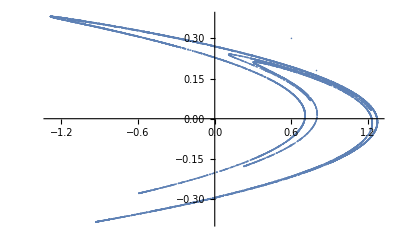

```mathematica
ListPlot[{x@#,y@#}&/@Range@10000]
```